```mathematica
(* WALKING KINEMATICS: HINDLIMB JOINT ANGLE PLOTS - Filtered, Archive data*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(*This code requires the data outputs from WALKING KINEMATICS: STICK FIGURE PLUS 3D JOINT ANGLES.nb. This code looks at all trials simultaneously *)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(* Determine operating system *)

os=$OperatingSystem;
frogworkpath="C:\\YOUR FILE DIRECTORY HERE\\" (*Set your main file directory, not to the folder where raw or archived data are stored*)
(*e.g. frogworkpath="C:\\Users\\Documents\\"*)
(*for Mac users change "C:\\" to "\\Volumes\\"*)

(***********************************************************************************)

(* Import metadata*)
(*Set the directory where the METADATA.xlsx is saved*)

(*SET DIRECTORY*)
dataDirectory="YOUR DIRECTORY TO METADATA.xlsx FILE";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

importedmetadata=Import["METADATA.xlsx","Data"];
metadata=importedmetadata[[1,2;;24,All]];

(***********************************************************************************)

(* Metadata file map: Locate information *)

Framerate=metadata[[3,1]];
```

```mathematica
(******************************************************************************************)

(* Import the 3D joint angle data files created with WALKING KINEMATICS: STICK FIGURE PLUS 3D JOINT ANGLES.nb  *)

(*Set directory*)
dataDirectory="YOUR DIRECTORY FOR 3D JOINT ANGLE DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*Import data*)
(*Hip*)
Animal0Trial1Hip=Import["KM01_RUN_02_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial1Hip=Import["KM02_RUN_01_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial2Hip=Import["KM02_RUN_02_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial3Hip=Import["KM02_RUN_09_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial1Hip=Import["KM04_RUN_09_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial2Hip=Import["KM04_RUN_11_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial3Hip=Import["KM04_RUN_12_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial1Hip=Import["KM05_RUN_04_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial2Hip=Import["KM05_RUN_08_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial1Hip=Import["KM06_RUN_11_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial2Hip=Import["KM06_RUN_12_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial3Hip=Import["KM06_RUN_13_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial4Hip=Import["KM06_RUN_15_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial5Hip=Import["KM06_RUN_16_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial1Hip=Import["KM07_RUN_14_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial2Hip=Import["KM07_RUN_16_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial3Hip=Import["KM07_RUN_17_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial1Hip=Import["KM08_RUN_09_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial2Hip=Import["KM08_RUN_10_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial1Hip=Import["KM23_RUN_01_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial2Hip=Import["KM23_RUN_02_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];Animal7Trial3Hip=Import["KM23_RUN_03_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial4Hip=Import["KM23_RUN_05_Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];

(*Knee*)
Animal0Trial1Knee=Import["KM01_RUN_02_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial1Knee=Import["KM02_RUN_01_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial2Knee=Import["KM02_RUN_02_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial3Knee=Import["KM02_RUN_09_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial1Knee=Import["KM04_RUN_09_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial2Knee=Import["KM04_RUN_11_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial3Knee=Import["KM04_RUN_12_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial1Knee=Import["KM05_RUN_04_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial2Knee=Import["KM05_RUN_08_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial1Knee=Import["KM06_RUN_11_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial2Knee=Import["KM06_RUN_12_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial3Knee=Import["KM06_RUN_13_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial4Knee=Import["KM06_RUN_15_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial5Knee=Import["KM06_RUN_16_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial1Knee=Import["KM07_RUN_14_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial2Knee=Import["KM07_RUN_16_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial3Knee=Import["KM07_RUN_17_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial1Knee=Import["KM08_RUN_09_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial2Knee=Import["KM08_RUN_10_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial1Knee=Import["KM23_RUN_01_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial2Knee=Import["KM23_RUN_02_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];Animal7Trial3Knee=Import["KM23_RUN_03_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial4Knee=Import["KM23_RUN_05_Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];

(*Ankle*)
Animal0Trial1Ankle=Import["KM01_RUN_02_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial1Ankle=Import["KM02_RUN_01_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial2Ankle=Import["KM02_RUN_02_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial3Ankle=Import["KM02_RUN_09_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial1Ankle=Import["KM04_RUN_09_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial2Ankle=Import["KM04_RUN_11_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial3Ankle=Import["KM04_RUN_12_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial1Ankle=Import["KM05_RUN_04_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial2Ankle=Import["KM05_RUN_08_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial1Ankle=Import["KM06_RUN_11_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial2Ankle=Import["KM06_RUN_12_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial3Ankle=Import["KM06_RUN_13_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial4Ankle=Import["KM06_RUN_15_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial5Ankle=Import["KM06_RUN_16_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial1Ankle=Import["KM07_RUN_14_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial2Ankle=Import["KM07_RUN_16_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial3Ankle=Import["KM07_RUN_17_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial1Ankle=Import["KM08_RUN_09_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial2Ankle=Import["KM08_RUN_10_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial1Ankle=Import["KM23_RUN_01_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial2Ankle=Import["KM23_RUN_02_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];Animal7Trial3Ankle=Import["KM23_RUN_03_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial4Ankle=Import["KM23_RUN_05_Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
(*************************************************************************************************************)

(* Import the Hip component joint angle data files created with WALKING KINEMATICS: STICK FIGURE PLUS 3D JOINT ANGLES.nb  *)

(*Set directory*)
dataDirectory="YOUR DIRECTORY FOR HIP COMPONENT JOINT ANGLE DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*Import data*)
(*HipXY*)
Animal0Trial1HipXY=Import["KM01_RUN_02_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial1HipXY=Import["KM02_RUN_01_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial2HipXY=Import["KM02_RUN_02_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial3HipXY=Import["KM02_RUN_09_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial1HipXY=Import["KM04_RUN_09_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial2HipXY=Import["KM04_RUN_11_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial3HipXY=Import["KM04_RUN_12_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial1HipXY=Import["KM05_RUN_04_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial2HipXY=Import["KM05_RUN_08_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial1HipXY=Import["KM06_RUN_11_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial2HipXY=Import["KM06_RUN_12_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial3HipXY=Import["KM06_RUN_13_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial4HipXY=Import["KM06_RUN_15_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial5HipXY=Import["KM06_RUN_16_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial1HipXY=Import["KM07_RUN_14_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial2HipXY=Import["KM07_RUN_16_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial3HipXY=Import["KM07_RUN_17_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial1HipXY=Import["KM08_RUN_09_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial2HipXY=Import["KM08_RUN_10_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial1HipXY=Import["KM23_RUN_01_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial2HipXY=Import["KM23_RUN_02_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];Animal7Trial3HipXY=Import["KM23_RUN_03_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial4HipXY=Import["KM23_RUN_05_Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];

(*HipYZ*)
Animal0Trial1HipYZ=Import["KM01_RUN_02_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial1HipYZ=Import["KM02_RUN_01_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial2HipYZ=Import["KM02_RUN_02_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial3HipYZ=Import["KM02_RUN_09_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial1HipYZ=Import["KM04_RUN_09_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial2HipYZ=Import["KM04_RUN_11_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial3HipYZ=Import["KM04_RUN_12_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial1HipYZ=Import["KM05_RUN_04_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial2HipYZ=Import["KM05_RUN_08_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial1HipYZ=Import["KM06_RUN_11_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial2HipYZ=Import["KM06_RUN_12_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial3HipYZ=Import["KM06_RUN_13_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial4HipYZ=Import["KM06_RUN_15_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial5HipYZ=Import["KM06_RUN_16_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial1HipYZ=Import["KM07_RUN_14_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial2HipYZ=Import["KM07_RUN_16_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial3HipYZ=Import["KM07_RUN_17_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial1HipYZ=Import["KM08_RUN_09_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial2HipYZ=Import["KM08_RUN_10_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial1HipYZ=Import["KM23_RUN_01_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial2HipYZ=Import["KM23_RUN_02_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];Animal7Trial3HipYZ=Import["KM23_RUN_03_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial4HipYZ=Import["KM23_RUN_05_Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

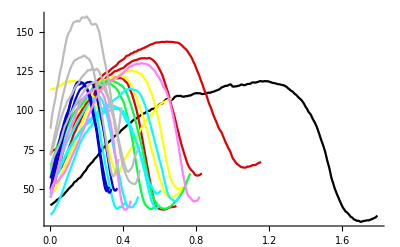

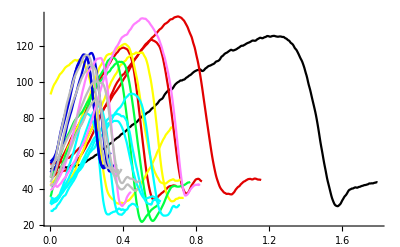

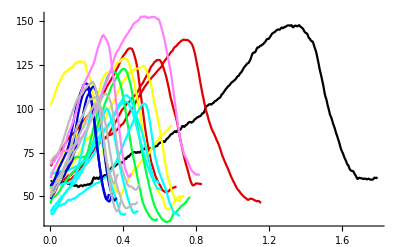

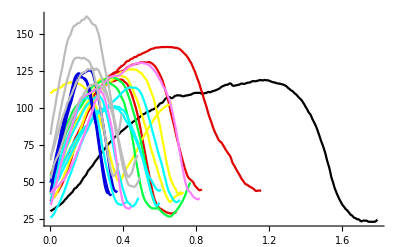

-Graphics-

```mathematica
(* Create plots *)

(* Absolute times*)

(*Plot style*)


ZERO=Setting[0.];
ONE=Setting[0.8823529411764706];
TWO=Setting[1.];
THREE=Setting[0.];
FOUR=Setting[0.];
FIVE=Setting[0.];
SIX=Setting[1.];
SEVEN = Setting[0.7372549019607844];

(*Hip*)
Animal0Trial1HipPlot=ListLinePlot[Animal0Trial1Hip,PlotStyle->ZERO];
Animal1Trial1HipPlot=ListLinePlot[Animal1Trial1Hip,PlotStyle->ONE];
Animal1Trial2HipPlot=ListLinePlot[Animal1Trial2Hip,PlotStyle->ONE];
Animal1Trial3HipPlot=ListLinePlot[Animal1Trial3Hip,PlotStyle->ONE];
Animal2Trial1HipPlot=ListLinePlot[Animal2Trial1Hip,PlotStyle->TWO];
Animal2Trial2HipPlot=ListLinePlot[Animal2Trial2Hip,PlotStyle->TWO];
Animal2Trial3HipPlot=ListLinePlot[Animal2Trial3Hip,PlotStyle->TWO];
Animal3Trial1HipPlot=ListLinePlot[Animal3Trial1Hip,PlotStyle->THREE];
Animal3Trial2HipPlot=ListLinePlot[Animal3Trial2Hip,PlotStyle->THREE];
Animal4Trial1HipPlot=ListLinePlot[Animal4Trial1Hip,PlotStyle->FOUR];
Animal4Trial2HipPlot=ListLinePlot[Animal4Trial2Hip,PlotStyle->FOUR];
Animal4Trial3HipPlot=ListLinePlot[Animal4Trial3Hip,PlotStyle->FOUR];
Animal4Trial4HipPlot=ListLinePlot[Animal4Trial4Hip,PlotStyle->FOUR];
Animal4Trial5HipPlot=ListLinePlot[Animal4Trial5Hip,PlotStyle->FOUR];
Animal5Trial1HipPlot=ListLinePlot[Animal5Trial1Hip,PlotStyle->FIVE];
Animal5Trial2HipPlot=ListLinePlot[Animal5Trial2Hip,PlotStyle->FIVE];
Animal5Trial3HipPlot=ListLinePlot[Animal5Trial3Hip,PlotStyle->FIVE];
Animal6Trial1HipPlot=ListLinePlot[Animal6Trial1Hip,PlotStyle->SIX];
Animal6Trial2HipPlot=ListLinePlot[Animal6Trial2Hip,PlotStyle->SIX];
Animal7Trial1HipPlot=ListLinePlot[Animal7Trial1Hip,PlotStyle->SEVEN];
Animal7Trial2HipPlot=ListLinePlot[Animal7Trial2Hip,PlotStyle->SEVEN];
Animal7Trial3HipPlot=ListLinePlot[Animal7Trial3Hip,PlotStyle->SEVEN];
Animal7Trial4HipPlot=ListLinePlot[Animal7Trial4Hip,PlotStyle->SEVEN];

AllAnimal0HipPlot=Show[Animal0Trial1HipPlot];
AllAnimal1HipPlot=Show[Animal1Trial1HipPlot,Animal1Trial2HipPlot,Animal1Trial3HipPlot];
AllAnimal2HipPlot=Show[Animal2Trial1HipPlot,Animal2Trial2HipPlot,Animal2Trial3HipPlot];
AllAnimal3HipPlot=Show[Animal3Trial1HipPlot,Animal3Trial2HipPlot];
AllAnimal4HipPlot=Show[Animal4Trial1HipPlot,Animal4Trial2HipPlot,Animal4Trial3HipPlot,Animal4Trial4HipPlot,Animal4Trial5HipPlot];
AllAnimal5HipPlot=Show[Animal5Trial1HipPlot,Animal5Trial2HipPlot,Animal5Trial3HipPlot];
AllAnimal6HipPlot=Show[Animal6Trial1HipPlot,Animal6Trial2HipPlot,PlotRange->All];
AllAnimal7HipPlot=Show[Animal7Trial1HipPlot,Animal7Trial2HipPlot,Animal7Trial3HipPlot,Animal7Trial4HipPlot];
AllAnimalsAllTrialsHip=Show[AllAnimal0HipPlot,AllAnimal1HipPlot,AllAnimal2HipPlot,AllAnimal3HipPlot,AllAnimal4HipPlot,AllAnimal5HipPlot,AllAnimal6HipPlot,AllAnimal7HipPlot,PlotRange->All]

(*Knee*)
Animal0Trial1KneePlot=ListLinePlot[Animal0Trial1Knee,PlotStyle->ZERO];
Animal1Trial1KneePlot=ListLinePlot[Animal1Trial1Knee,PlotStyle->ONE];
Animal1Trial2KneePlot=ListLinePlot[Animal1Trial2Knee,PlotStyle->ONE];
Animal1Trial3KneePlot=ListLinePlot[Animal1Trial3Knee,PlotStyle->ONE];
Animal2Trial1KneePlot=ListLinePlot[Animal2Trial1Knee,PlotStyle->TWO];
Animal2Trial2KneePlot=ListLinePlot[Animal2Trial2Knee,PlotStyle->TWO];
Animal2Trial3KneePlot=ListLinePlot[Animal2Trial3Knee,PlotStyle->TWO];
Animal3Trial1KneePlot=ListLinePlot[Animal3Trial1Knee,PlotStyle->THREE];
Animal3Trial2KneePlot=ListLinePlot[Animal3Trial2Knee,PlotStyle->THREE];
Animal4Trial1KneePlot=ListLinePlot[Animal4Trial1Knee,PlotStyle->FOUR];
Animal4Trial2KneePlot=ListLinePlot[Animal4Trial2Knee,PlotStyle->FOUR];
Animal4Trial3KneePlot=ListLinePlot[Animal4Trial3Knee,PlotStyle->FOUR];
Animal4Trial4KneePlot=ListLinePlot[Animal4Trial4Knee,PlotStyle->FOUR];
Animal4Trial5KneePlot=ListLinePlot[Animal4Trial5Knee,PlotStyle->FOUR];
Animal5Trial1KneePlot=ListLinePlot[Animal5Trial1Knee,PlotStyle->FIVE];
Animal5Trial2KneePlot=ListLinePlot[Animal5Trial2Knee,PlotStyle->FIVE];
Animal5Trial3KneePlot=ListLinePlot[Animal5Trial3Knee,PlotStyle->FIVE];
Animal6Trial1KneePlot=ListLinePlot[Animal6Trial1Knee,PlotStyle->SIX];
Animal6Trial2KneePlot=ListLinePlot[Animal6Trial2Knee,PlotStyle->SIX];
Animal7Trial1KneePlot=ListLinePlot[Animal7Trial1Knee,PlotStyle->SEVEN];
Animal7Trial2KneePlot=ListLinePlot[Animal7Trial2Knee,PlotStyle->SEVEN];
Animal7Trial3KneePlot=ListLinePlot[Animal7Trial3Knee,PlotStyle->SEVEN];
Animal7Trial4KneePlot=ListLinePlot[Animal7Trial4Knee,PlotStyle->SEVEN];

AllAnimal0KneePlot=Show[Animal0Trial1KneePlot];
AllAnimal1KneePlot=Show[Animal1Trial1KneePlot,Animal1Trial2KneePlot,Animal1Trial3KneePlot];
AllAnimal2KneePlot=Show[Animal2Trial1KneePlot,Animal2Trial2KneePlot,Animal2Trial3KneePlot];
AllAnimal3KneePlot=Show[Animal3Trial1KneePlot,Animal3Trial2KneePlot];
AllAnimal4KneePlot=Show[Animal4Trial1KneePlot,Animal4Trial2KneePlot,Animal4Trial3KneePlot,Animal4Trial4KneePlot,Animal4Trial5KneePlot];
AllAnimal5KneePlot=Show[Animal5Trial1KneePlot,Animal5Trial2KneePlot,Animal5Trial3KneePlot];
AllAnimal6KneePlot=Show[Animal6Trial1KneePlot,Animal6Trial2KneePlot,PlotRange->All];
AllAnimal7KneePlot=Show[Animal7Trial1KneePlot,Animal7Trial2KneePlot,Animal7Trial3KneePlot,Animal7Trial4KneePlot];
AllAnimalsAllTrialsKnee=Show[AllAnimal0KneePlot,AllAnimal1KneePlot,AllAnimal2KneePlot,AllAnimal3KneePlot,AllAnimal4KneePlot,AllAnimal5KneePlot,AllAnimal6KneePlot,AllAnimal7KneePlot,PlotRange->All]

(*Ankle*)
Animal0Trial1AnklePlot=ListLinePlot[Animal0Trial1Ankle,PlotStyle->ZERO];
Animal1Trial1AnklePlot=ListLinePlot[Animal1Trial1Ankle,PlotStyle->ONE];
Animal1Trial2AnklePlot=ListLinePlot[Animal1Trial2Ankle,PlotStyle->ONE];
Animal1Trial3AnklePlot=ListLinePlot[Animal1Trial3Ankle,PlotStyle->ONE];
Animal2Trial1AnklePlot=ListLinePlot[Animal2Trial1Ankle,PlotStyle->TWO];
Animal2Trial2AnklePlot=ListLinePlot[Animal2Trial2Ankle,PlotStyle->TWO];
Animal2Trial3AnklePlot=ListLinePlot[Animal2Trial3Ankle,PlotStyle->TWO];
Animal3Trial1AnklePlot=ListLinePlot[Animal3Trial1Ankle,PlotStyle->THREE];
Animal3Trial2AnklePlot=ListLinePlot[Animal3Trial2Ankle,PlotStyle->THREE];
Animal4Trial1AnklePlot=ListLinePlot[Animal4Trial1Ankle,PlotStyle->FOUR];
Animal4Trial2AnklePlot=ListLinePlot[Animal4Trial2Ankle,PlotStyle->FOUR];
Animal4Trial3AnklePlot=ListLinePlot[Animal4Trial3Ankle,PlotStyle->FOUR];
Animal4Trial4AnklePlot=ListLinePlot[Animal4Trial4Ankle,PlotStyle->FOUR];
Animal4Trial5AnklePlot=ListLinePlot[Animal4Trial5Ankle,PlotStyle->FOUR];
Animal5Trial1AnklePlot=ListLinePlot[Animal5Trial1Ankle,PlotStyle->FIVE];
Animal5Trial2AnklePlot=ListLinePlot[Animal5Trial2Ankle,PlotStyle->FIVE];
Animal5Trial3AnklePlot=ListLinePlot[Animal5Trial3Ankle,PlotStyle->FIVE];
Animal6Trial1AnklePlot=ListLinePlot[Animal6Trial1Ankle,PlotStyle->SIX];
Animal6Trial2AnklePlot=ListLinePlot[Animal6Trial2Ankle,PlotStyle->SIX];
Animal7Trial1AnklePlot=ListLinePlot[Animal7Trial1Ankle,PlotStyle->SEVEN];
Animal7Trial2AnklePlot=ListLinePlot[Animal7Trial2Ankle,PlotStyle->SEVEN];
Animal7Trial3AnklePlot=ListLinePlot[Animal7Trial3Ankle,PlotStyle->SEVEN];
Animal7Trial4AnklePlot=ListLinePlot[Animal7Trial4Ankle,PlotStyle->SEVEN];

AllAnimal0AnklePlot=Show[Animal0Trial1AnklePlot];
AllAnimal1AnklePlot=Show[Animal1Trial1AnklePlot,Animal1Trial2AnklePlot,Animal1Trial3AnklePlot];
AllAnimal2AnklePlot=Show[Animal2Trial1AnklePlot,Animal2Trial2AnklePlot,Animal2Trial3AnklePlot];
AllAnimal3AnklePlot=Show[Animal3Trial1AnklePlot,Animal3Trial2AnklePlot];
AllAnimal4AnklePlot=Show[Animal4Trial1AnklePlot,Animal4Trial2AnklePlot,Animal4Trial3AnklePlot,Animal4Trial4AnklePlot,Animal4Trial5AnklePlot];
AllAnimal5AnklePlot=Show[Animal5Trial1AnklePlot,Animal5Trial2AnklePlot,Animal5Trial3AnklePlot];
AllAnimal6AnklePlot=Show[Animal6Trial1AnklePlot,Animal6Trial2AnklePlot,PlotRange->All];
AllAnimal7AnklePlot=Show[Animal7Trial1AnklePlot,Animal7Trial2AnklePlot,Animal7Trial3AnklePlot,Animal7Trial4AnklePlot];
AllAnimalsAllTrialsAnkle=Show[AllAnimal0AnklePlot,AllAnimal1AnklePlot,AllAnimal2AnklePlot,AllAnimal3AnklePlot,AllAnimal4AnklePlot,AllAnimal5AnklePlot,AllAnimal6AnklePlot,AllAnimal7AnklePlot,PlotRange->All]

(*HipXY*)
Animal0Trial1HipXYPlot=ListLinePlot[Animal0Trial1HipXY,PlotStyle->ZERO];
Animal1Trial1HipXYPlot=ListLinePlot[Animal1Trial1HipXY,PlotStyle->ONE];
Animal1Trial2HipXYPlot=ListLinePlot[Animal1Trial2HipXY,PlotStyle->ONE];
Animal1Trial3HipXYPlot=ListLinePlot[Animal1Trial3HipXY,PlotStyle->ONE];
Animal2Trial1HipXYPlot=ListLinePlot[Animal2Trial1HipXY,PlotStyle->TWO];
Animal2Trial2HipXYPlot=ListLinePlot[Animal2Trial2HipXY,PlotStyle->TWO];
Animal2Trial3HipXYPlot=ListLinePlot[Animal2Trial3HipXY,PlotStyle->TWO];
Animal3Trial1HipXYPlot=ListLinePlot[Animal3Trial1HipXY,PlotStyle->THREE];
Animal3Trial2HipXYPlot=ListLinePlot[Animal3Trial2HipXY,PlotStyle->THREE];
Animal4Trial1HipXYPlot=ListLinePlot[Animal4Trial1HipXY,PlotStyle->FOUR];
Animal4Trial2HipXYPlot=ListLinePlot[Animal4Trial2HipXY,PlotStyle->FOUR];
Animal4Trial3HipXYPlot=ListLinePlot[Animal4Trial3HipXY,PlotStyle->FOUR];
Animal4Trial4HipXYPlot=ListLinePlot[Animal4Trial4HipXY,PlotStyle->FOUR];
Animal4Trial5HipXYPlot=ListLinePlot[Animal4Trial5HipXY,PlotStyle->FOUR];
Animal5Trial1HipXYPlot=ListLinePlot[Animal5Trial1HipXY,PlotStyle->FIVE];
Animal5Trial2HipXYPlot=ListLinePlot[Animal5Trial2HipXY,PlotStyle->FIVE];
Animal5Trial3HipXYPlot=ListLinePlot[Animal5Trial3HipXY,PlotStyle->FIVE];
Animal6Trial1HipXYPlot=ListLinePlot[Animal6Trial1HipXY,PlotStyle->SIX];
Animal6Trial2HipXYPlot=ListLinePlot[Animal6Trial2HipXY,PlotStyle->SIX];
Animal7Trial1HipXYPlot=ListLinePlot[Animal7Trial1HipXY,PlotStyle->SEVEN];
Animal7Trial2HipXYPlot=ListLinePlot[Animal7Trial2HipXY,PlotStyle->SEVEN];
Animal7Trial3HipXYPlot=ListLinePlot[Animal7Trial3HipXY,PlotStyle->SEVEN];
Animal7Trial4HipXYPlot=ListLinePlot[Animal7Trial4HipXY,PlotStyle->SEVEN];

AllAnimal0HipXYPlot=Show[Animal0Trial1HipXYPlot];
AllAnimal1HipXYPlot=Show[Animal1Trial1HipXYPlot,Animal1Trial2HipXYPlot,Animal1Trial3HipXYPlot];
AllAnimal2HipXYPlot=Show[Animal2Trial1HipXYPlot,Animal2Trial2HipXYPlot,Animal2Trial3HipXYPlot];
AllAnimal3HipXYPlot=Show[Animal3Trial1HipXYPlot,Animal3Trial2HipXYPlot];
AllAnimal4HipXYPlot=Show[Animal4Trial1HipXYPlot,Animal4Trial2HipXYPlot,Animal4Trial3HipXYPlot,Animal4Trial4HipXYPlot,Animal4Trial5HipXYPlot];
AllAnimal5HipXYPlot=Show[Animal5Trial1HipXYPlot,Animal5Trial2HipXYPlot,Animal5Trial3HipXYPlot];
AllAnimal6HipXYPlot=Show[Animal6Trial1HipXYPlot,Animal6Trial2HipXYPlot,PlotRange->All];
AllAnimal7HipXYPlot=Show[Animal7Trial1HipXYPlot,Animal7Trial2HipXYPlot,Animal7Trial3HipXYPlot,Animal7Trial4HipXYPlot];
AllAnimalsAllTrialsHipXY=Show[AllAnimal0HipXYPlot,AllAnimal1HipXYPlot,AllAnimal2HipXYPlot,AllAnimal3HipXYPlot,AllAnimal4HipXYPlot,AllAnimal5HipXYPlot,AllAnimal6HipXYPlot,AllAnimal7HipXYPlot,PlotRange->All]

(*HipYZ*)
Animal0Trial1HipYZPlot=ListLinePlot[Animal0Trial1HipYZ,PlotStyle->ZERO];
Animal1Trial1HipYZPlot=ListLinePlot[Animal1Trial1HipYZ,PlotStyle->ONE];
Animal1Trial2HipYZPlot=ListLinePlot[Animal1Trial2HipYZ,PlotStyle->ONE];
Animal1Trial3HipYZPlot=ListLinePlot[Animal1Trial3HipYZ,PlotStyle->ONE];
Animal2Trial1HipYZPlot=ListLinePlot[Animal2Trial1HipYZ,PlotStyle->TWO];
Animal2Trial2HipYZPlot=ListLinePlot[Animal2Trial2HipYZ,PlotStyle->TWO];
Animal2Trial3HipYZPlot=ListLinePlot[Animal2Trial3HipYZ,PlotStyle->TWO];
Animal3Trial1HipYZPlot=ListLinePlot[Animal3Trial1HipYZ,PlotStyle->THREE];
Animal3Trial2HipYZPlot=ListLinePlot[Animal3Trial2HipYZ,PlotStyle->THREE];
Animal4Trial1HipYZPlot=ListLinePlot[Animal4Trial1HipYZ,PlotStyle->FOUR];
Animal4Trial2HipYZPlot=ListLinePlot[Animal4Trial2HipYZ,PlotStyle->FOUR];
Animal4Trial3HipYZPlot=ListLinePlot[Animal4Trial3HipYZ,PlotStyle->FOUR];
Animal4Trial4HipYZPlot=ListLinePlot[Animal4Trial4HipYZ,PlotStyle->FOUR];
Animal4Trial5HipYZPlot=ListLinePlot[Animal4Trial5HipYZ,PlotStyle->FOUR];
Animal5Trial1HipYZPlot=ListLinePlot[Animal5Trial1HipYZ,PlotStyle->FIVE];
Animal5Trial2HipYZPlot=ListLinePlot[Animal5Trial2HipYZ,PlotStyle->FIVE];
Animal5Trial3HipYZPlot=ListLinePlot[Animal5Trial3HipYZ,PlotStyle->FIVE];
Animal6Trial1HipYZPlot=ListLinePlot[Animal6Trial1HipYZ,PlotStyle->SIX];
Animal6Trial2HipYZPlot=ListLinePlot[Animal6Trial2HipYZ,PlotStyle->SIX];
Animal7Trial1HipYZPlot=ListLinePlot[Animal7Trial1HipYZ,PlotStyle->SEVEN];
Animal7Trial2HipYZPlot=ListLinePlot[Animal7Trial2HipYZ,PlotStyle->SEVEN];
Animal7Trial3HipYZPlot=ListLinePlot[Animal7Trial3HipYZ,PlotStyle->SEVEN];
Animal7Trial4HipYZPlot=ListLinePlot[Animal7Trial4HipYZ,PlotStyle->SEVEN];

(*AllAnimal0HipYZPlot=Show[Animal0Trial1HipYZPlot];
AllAnimal1HipYZPlot=Show[Animal1Trial1HipYZPlot,Animal1Trial2HipYZPlot,Animal1Trial3HipYZPlot];
AllAnimal2HipYZPlot=Show[Animal2Trial1HipYZPlot,Animal2Trial2HipYZPlot,Animal2Trial3HipYZPlot];
AllAnimal3HipYZPlot=Show[Animal3Trial1HipYZPlot,Animal3Trial2HipYZPlot];
AllAnimal4HipYZPlot=Show[Animal4Trial1HipYZPlot,Animal4Trial2HipYZPlot,Animal4Trial3HipYZPlot,Animal4Trial4HipYZPlot,Animal4Trial5HipYZPlot];
AllAnimal5HipYZPlot=Show[Animal5Trial1HipYZPlot,Animal5Trial2HipYZPlot,Animal5Trial3HipYZPlot];
AllAnimal6HipYZPlot=Show[Animal6Trial1HipYZPlot,Animal6Trial2HipYZPlot,PlotRange->All];
AllAnimal7HipYZPlot=Show[Animal7Trial1HipYZPlot,Animal7Trial2HipYZPlot,Animal7Trial3HipYZPlot,Animal7Trial4HipYZPlot];
AllAnimalsAllTrialsHipYZ=Show[AllAnimal0HipYZPlot,AllAnimal1HipYZPlot,AllAnimal2HipYZPlot,AllAnimal3HipYZPlot,AllAnimal4HipYZPlot,AllAnimal5HipYZPlot,AllAnimal6HipYZPlot,AllAnimal7HipYZPlot,PlotRange->All]*)
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

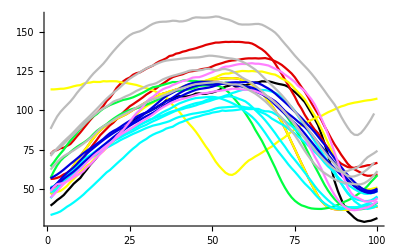

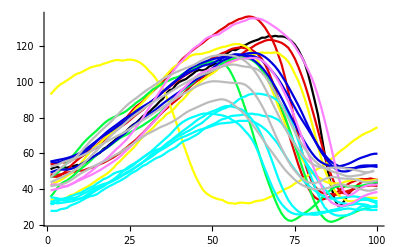

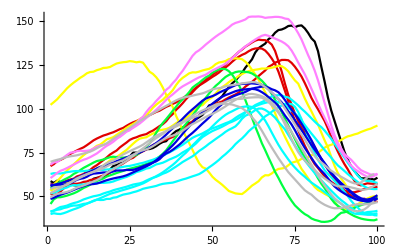

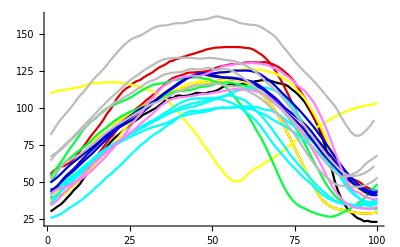

-Graphics-

```mathematica
(* Time normalise the data *)

(* Define length of each trial - used hip only since trails are the same length for each joint*)

LengthAnimal0Trial1=Length[Animal0Trial1Hip[[1,All]]];
LengthAnimal1Trial1=Length[Animal1Trial1Hip[[1,All]]];
LengthAnimal1Trial2=Length[Animal1Trial2Hip[[1,All]]];
LengthAnimal1Trial3=Length[Animal1Trial3Hip[[1,All]]];
LengthAnimal2Trial1=Length[Animal2Trial1Hip[[1,All]]];
LengthAnimal2Trial2=Length[Animal2Trial2Hip[[1,All]]];
LengthAnimal2Trial3=Length[Animal2Trial3Hip[[1,All]]];
LengthAnimal3Trial1=Length[Animal3Trial1Hip[[1,All]]];
LengthAnimal3Trial2=Length[Animal3Trial2Hip[[1,All]]];
LengthAnimal4Trial1=Length[Animal4Trial1Hip[[1,All]]];
LengthAnimal4Trial2=Length[Animal4Trial2Hip[[1,All]]];
LengthAnimal4Trial3=Length[Animal4Trial3Hip[[1,All]]];
LengthAnimal4Trial4=Length[Animal4Trial4Hip[[1,All]]];
LengthAnimal4Trial5=Length[Animal4Trial5Hip[[1,All]]];
LengthAnimal5Trial1=Length[Animal5Trial1Hip[[1,All]]];
LengthAnimal5Trial2=Length[Animal5Trial2Hip[[1,All]]];
LengthAnimal5Trial3=Length[Animal5Trial3Hip[[1,All]]];
LengthAnimal6Trial1=Length[Animal6Trial1Hip[[1,All]]];
LengthAnimal6Trial2=Length[Animal6Trial2Hip[[1,All]]];
LengthAnimal7Trial1=Length[Animal7Trial1Hip[[1,All]]];
LengthAnimal7Trial2=Length[Animal7Trial2Hip[[1,All]]];
LengthAnimal7Trial3=Length[Animal7Trial3Hip[[1,All]]];
LengthAnimal7Trial4=Length[Animal7Trial4Hip[[1,All]]];

(* Set desired number of data points - Number of points is the same as LengthAnimal?Trial?*)

DesiredLengthofData=100;

(******************************************************************************************)

(*Get just the angle data*)

(*Hip*)
Animal0Trial1HipAngle=Animal0Trial1Hip[[1,All,2]];
Animal1Trial1HipAngle=Animal1Trial1Hip[[1,All,2]];
Animal1Trial2HipAngle=Animal1Trial2Hip[[1,All,2]];
Animal1Trial3HipAngle=Animal1Trial3Hip[[1,All,2]];
Animal2Trial1HipAngle=Animal2Trial1Hip[[1,All,2]];
Animal2Trial2HipAngle=Animal2Trial2Hip[[1,All,2]];
Animal2Trial3HipAngle=Animal2Trial3Hip[[1,All,2]];
Animal3Trial1HipAngle=Animal3Trial1Hip[[1,All,2]];
Animal3Trial2HipAngle=Animal3Trial2Hip[[1,All,2]];
Animal4Trial1HipAngle=Animal4Trial1Hip[[1,All,2]];
Animal4Trial2HipAngle=Animal4Trial2Hip[[1,All,2]];
Animal4Trial3HipAngle=Animal4Trial3Hip[[1,All,2]];
Animal4Trial4HipAngle=Animal4Trial4Hip[[1,All,2]];
Animal4Trial5HipAngle=Animal4Trial5Hip[[1,All,2]];
Animal5Trial1HipAngle=Animal5Trial1Hip[[1,All,2]];
Animal5Trial2HipAngle=Animal5Trial2Hip[[1,All,2]];
Animal5Trial3HipAngle=Animal5Trial3Hip[[1,All,2]];
Animal6Trial1HipAngle=Animal6Trial1Hip[[1,All,2]];
Animal6Trial2HipAngle=Animal6Trial2Hip[[1,All,2]];
Animal7Trial1HipAngle=Animal7Trial1Hip[[1,All,2]];
Animal7Trial2HipAngle=Animal7Trial2Hip[[1,All,2]];
Animal7Trial3HipAngle=Animal7Trial3Hip[[1,All,2]];
Animal7Trial4HipAngle=Animal7Trial4Hip[[1,All,2]];

(*Knee*)
Animal0Trial1KneeAngle=Animal0Trial1Knee[[1,All,2]];
Animal1Trial1KneeAngle=Animal1Trial1Knee[[1,All,2]];
Animal1Trial2KneeAngle=Animal1Trial2Knee[[1,All,2]];
Animal1Trial3KneeAngle=Animal1Trial3Knee[[1,All,2]];
Animal2Trial1KneeAngle=Animal2Trial1Knee[[1,All,2]];
Animal2Trial2KneeAngle=Animal2Trial2Knee[[1,All,2]];
Animal2Trial3KneeAngle=Animal2Trial3Knee[[1,All,2]];
Animal3Trial1KneeAngle=Animal3Trial1Knee[[1,All,2]];
Animal3Trial2KneeAngle=Animal3Trial2Knee[[1,All,2]];
Animal4Trial1KneeAngle=Animal4Trial1Knee[[1,All,2]];
Animal4Trial2KneeAngle=Animal4Trial2Knee[[1,All,2]];
Animal4Trial3KneeAngle=Animal4Trial3Knee[[1,All,2]];
Animal4Trial4KneeAngle=Animal4Trial4Knee[[1,All,2]];
Animal4Trial5KneeAngle=Animal4Trial5Knee[[1,All,2]];
Animal5Trial1KneeAngle=Animal5Trial1Knee[[1,All,2]];
Animal5Trial2KneeAngle=Animal5Trial2Knee[[1,All,2]];
Animal5Trial3KneeAngle=Animal5Trial3Knee[[1,All,2]];
Animal6Trial1KneeAngle=Animal6Trial1Knee[[1,All,2]];
Animal6Trial2KneeAngle=Animal6Trial2Knee[[1,All,2]];
Animal7Trial1KneeAngle=Animal7Trial1Knee[[1,All,2]];
Animal7Trial2KneeAngle=Animal7Trial2Knee[[1,All,2]];
Animal7Trial3KneeAngle=Animal7Trial3Knee[[1,All,2]];
Animal7Trial4KneeAngle=Animal7Trial4Knee[[1,All,2]];

(*Ankle*)
Animal0Trial1AnkleAngle=Animal0Trial1Ankle[[1,All,2]];
Animal1Trial1AnkleAngle=Animal1Trial1Ankle[[1,All,2]];
Animal1Trial2AnkleAngle=Animal1Trial2Ankle[[1,All,2]];
Animal1Trial3AnkleAngle=Animal1Trial3Ankle[[1,All,2]];
Animal2Trial1AnkleAngle=Animal2Trial1Ankle[[1,All,2]];
Animal2Trial2AnkleAngle=Animal2Trial2Ankle[[1,All,2]];
Animal2Trial3AnkleAngle=Animal2Trial3Ankle[[1,All,2]];
Animal3Trial1AnkleAngle=Animal3Trial1Ankle[[1,All,2]];
Animal3Trial2AnkleAngle=Animal3Trial2Ankle[[1,All,2]];
Animal4Trial1AnkleAngle=Animal4Trial1Ankle[[1,All,2]];
Animal4Trial2AnkleAngle=Animal4Trial2Ankle[[1,All,2]];
Animal4Trial3AnkleAngle=Animal4Trial3Ankle[[1,All,2]];
Animal4Trial4AnkleAngle=Animal4Trial4Ankle[[1,All,2]];
Animal4Trial5AnkleAngle=Animal4Trial5Ankle[[1,All,2]];
Animal5Trial1AnkleAngle=Animal5Trial1Ankle[[1,All,2]];
Animal5Trial2AnkleAngle=Animal5Trial2Ankle[[1,All,2]];
Animal5Trial3AnkleAngle=Animal5Trial3Ankle[[1,All,2]];
Animal6Trial1AnkleAngle=Animal6Trial1Ankle[[1,All,2]];
Animal6Trial2AnkleAngle=Animal6Trial2Ankle[[1,All,2]];
Animal7Trial1AnkleAngle=Animal7Trial1Ankle[[1,All,2]];
Animal7Trial2AnkleAngle=Animal7Trial2Ankle[[1,All,2]];
Animal7Trial3AnkleAngle=Animal7Trial3Ankle[[1,All,2]];
Animal7Trial4AnkleAngle=Animal7Trial4Ankle[[1,All,2]];

(*HipXY*)
Animal0Trial1HipXYAngle=Animal0Trial1HipXY[[1,All,2]];
Animal1Trial1HipXYAngle=Animal1Trial1HipXY[[1,All,2]];
Animal1Trial2HipXYAngle=Animal1Trial2HipXY[[1,All,2]];
Animal1Trial3HipXYAngle=Animal1Trial3HipXY[[1,All,2]];
Animal2Trial1HipXYAngle=Animal2Trial1HipXY[[1,All,2]];
Animal2Trial2HipXYAngle=Animal2Trial2HipXY[[1,All,2]];
Animal2Trial3HipXYAngle=Animal2Trial3HipXY[[1,All,2]];
Animal3Trial1HipXYAngle=Animal3Trial1HipXY[[1,All,2]];
Animal3Trial2HipXYAngle=Animal3Trial2HipXY[[1,All,2]];
Animal4Trial1HipXYAngle=Animal4Trial1HipXY[[1,All,2]];
Animal4Trial2HipXYAngle=Animal4Trial2HipXY[[1,All,2]];
Animal4Trial3HipXYAngle=Animal4Trial3HipXY[[1,All,2]];
Animal4Trial4HipXYAngle=Animal4Trial4HipXY[[1,All,2]];
Animal4Trial5HipXYAngle=Animal4Trial5HipXY[[1,All,2]];
Animal5Trial1HipXYAngle=Animal5Trial1HipXY[[1,All,2]];
Animal5Trial2HipXYAngle=Animal5Trial2HipXY[[1,All,2]];
Animal5Trial3HipXYAngle=Animal5Trial3HipXY[[1,All,2]];
Animal6Trial1HipXYAngle=Animal6Trial1HipXY[[1,All,2]];
Animal6Trial2HipXYAngle=Animal6Trial2HipXY[[1,All,2]];
Animal7Trial1HipXYAngle=Animal7Trial1HipXY[[1,All,2]];
Animal7Trial2HipXYAngle=Animal7Trial2HipXY[[1,All,2]];
Animal7Trial3HipXYAngle=Animal7Trial3HipXY[[1,All,2]];
Animal7Trial4HipXYAngle=Animal7Trial4HipXY[[1,All,2]];

(*HipYZ*)
Animal0Trial1HipYZAngle=Animal0Trial1HipYZ[[1,All,2]];
Animal1Trial1HipYZAngle=Animal1Trial1HipYZ[[1,All,2]];
Animal1Trial2HipYZAngle=Animal1Trial2HipYZ[[1,All,2]];
Animal1Trial3HipYZAngle=Animal1Trial3HipYZ[[1,All,2]];
Animal2Trial1HipYZAngle=Animal2Trial1HipYZ[[1,All,2]];
Animal2Trial2HipYZAngle=Animal2Trial2HipYZ[[1,All,2]];
Animal2Trial3HipYZAngle=Animal2Trial3HipYZ[[1,All,2]];
Animal3Trial1HipYZAngle=Animal3Trial1HipYZ[[1,All,2]];
Animal3Trial2HipYZAngle=Animal3Trial2HipYZ[[1,All,2]];
Animal4Trial1HipYZAngle=Animal4Trial1HipYZ[[1,All,2]];
Animal4Trial2HipYZAngle=Animal4Trial2HipYZ[[1,All,2]];
Animal4Trial3HipYZAngle=Animal4Trial3HipYZ[[1,All,2]];
Animal4Trial4HipYZAngle=Animal4Trial4HipYZ[[1,All,2]];
Animal4Trial5HipYZAngle=Animal4Trial5HipYZ[[1,All,2]];
Animal5Trial1HipYZAngle=Animal5Trial1HipYZ[[1,All,2]];
Animal5Trial2HipYZAngle=Animal5Trial2HipYZ[[1,All,2]];
Animal5Trial3HipYZAngle=Animal5Trial3HipYZ[[1,All,2]];
Animal6Trial1HipYZAngle=Animal6Trial1HipYZ[[1,All,2]];
Animal6Trial2HipYZAngle=Animal6Trial2HipYZ[[1,All,2]];
Animal7Trial1HipYZAngle=Animal7Trial1HipYZ[[1,All,2]];
Animal7Trial2HipYZAngle=Animal7Trial2HipYZ[[1,All,2]];
Animal7Trial3HipYZAngle=Animal7Trial3HipYZ[[1,All,2]];
Animal7Trial4HipYZAngle=Animal7Trial4HipYZ[[1,All,2]];

(******************************************************************************************)

(*1. Interpolate the data - I*)

(*Hip*)
IAnimal0Trial1Hip=Interpolation[Animal0Trial1HipAngle];
IAnimal1Trial1Hip=Interpolation[Animal1Trial1HipAngle];
IAnimal1Trial2Hip=Interpolation[Animal1Trial2HipAngle];
IAnimal1Trial3Hip=Interpolation[Animal1Trial3HipAngle];
IAnimal2Trial1Hip=Interpolation[Animal2Trial1HipAngle];
IAnimal2Trial2Hip=Interpolation[Animal2Trial2HipAngle];
IAnimal2Trial3Hip=Interpolation[Animal2Trial3HipAngle];
IAnimal3Trial1Hip=Interpolation[Animal3Trial1HipAngle];
IAnimal3Trial2Hip=Interpolation[Animal3Trial2HipAngle];
IAnimal4Trial1Hip=Interpolation[Animal4Trial1HipAngle];
IAnimal4Trial2Hip=Interpolation[Animal4Trial2HipAngle];
IAnimal4Trial3Hip=Interpolation[Animal4Trial3HipAngle];
IAnimal4Trial4Hip=Interpolation[Animal4Trial4HipAngle];
IAnimal4Trial5Hip=Interpolation[Animal4Trial5HipAngle];
IAnimal5Trial1Hip=Interpolation[Animal5Trial1HipAngle];
IAnimal5Trial2Hip=Interpolation[Animal5Trial2HipAngle];
IAnimal5Trial3Hip=Interpolation[Animal5Trial3HipAngle];
IAnimal6Trial1Hip=Interpolation[Animal6Trial1HipAngle];
IAnimal6Trial2Hip=Interpolation[Animal6Trial2HipAngle];
IAnimal7Trial1Hip=Interpolation[Animal7Trial1HipAngle];
IAnimal7Trial2Hip=Interpolation[Animal7Trial2HipAngle];
IAnimal7Trial3Hip=Interpolation[Animal7Trial3HipAngle];
IAnimal7Trial4Hip=Interpolation[Animal7Trial4HipAngle];

(*Knee*)
IAnimal0Trial1Knee=Interpolation[Animal0Trial1KneeAngle];
IAnimal1Trial1Knee=Interpolation[Animal1Trial1KneeAngle];
IAnimal1Trial2Knee=Interpolation[Animal1Trial2KneeAngle];
IAnimal1Trial3Knee=Interpolation[Animal1Trial3KneeAngle];
IAnimal2Trial1Knee=Interpolation[Animal2Trial1KneeAngle];
IAnimal2Trial2Knee=Interpolation[Animal2Trial2KneeAngle];
IAnimal2Trial3Knee=Interpolation[Animal2Trial3KneeAngle];
IAnimal3Trial1Knee=Interpolation[Animal3Trial1KneeAngle];
IAnimal3Trial2Knee=Interpolation[Animal3Trial2KneeAngle];
IAnimal4Trial1Knee=Interpolation[Animal4Trial1KneeAngle];
IAnimal4Trial2Knee=Interpolation[Animal4Trial2KneeAngle];
IAnimal4Trial3Knee=Interpolation[Animal4Trial3KneeAngle];
IAnimal4Trial4Knee=Interpolation[Animal4Trial4KneeAngle];
IAnimal4Trial5Knee=Interpolation[Animal4Trial5KneeAngle];
IAnimal5Trial1Knee=Interpolation[Animal5Trial1KneeAngle];
IAnimal5Trial2Knee=Interpolation[Animal5Trial2KneeAngle];
IAnimal5Trial3Knee=Interpolation[Animal5Trial3KneeAngle];
IAnimal6Trial1Knee=Interpolation[Animal6Trial1KneeAngle];
IAnimal6Trial2Knee=Interpolation[Animal6Trial2KneeAngle];
IAnimal7Trial1Knee=Interpolation[Animal7Trial1KneeAngle];
IAnimal7Trial2Knee=Interpolation[Animal7Trial2KneeAngle];
IAnimal7Trial3Knee=Interpolation[Animal7Trial3KneeAngle];
IAnimal7Trial4Knee=Interpolation[Animal7Trial4KneeAngle];

(*Ankle*)
IAnimal0Trial1Ankle=Interpolation[Animal0Trial1AnkleAngle];
IAnimal1Trial1Ankle=Interpolation[Animal1Trial1AnkleAngle];
IAnimal1Trial2Ankle=Interpolation[Animal1Trial2AnkleAngle];
IAnimal1Trial3Ankle=Interpolation[Animal1Trial3AnkleAngle];
IAnimal2Trial1Ankle=Interpolation[Animal2Trial1AnkleAngle];
IAnimal2Trial2Ankle=Interpolation[Animal2Trial2AnkleAngle];
IAnimal2Trial3Ankle=Interpolation[Animal2Trial3AnkleAngle];
IAnimal3Trial1Ankle=Interpolation[Animal3Trial1AnkleAngle];
IAnimal3Trial2Ankle=Interpolation[Animal3Trial2AnkleAngle];
IAnimal4Trial1Ankle=Interpolation[Animal4Trial1AnkleAngle];
IAnimal4Trial2Ankle=Interpolation[Animal4Trial2AnkleAngle];
IAnimal4Trial3Ankle=Interpolation[Animal4Trial3AnkleAngle];
IAnimal4Trial4Ankle=Interpolation[Animal4Trial4AnkleAngle];
IAnimal4Trial5Ankle=Interpolation[Animal4Trial5AnkleAngle];
IAnimal5Trial1Ankle=Interpolation[Animal5Trial1AnkleAngle];
IAnimal5Trial2Ankle=Interpolation[Animal5Trial2AnkleAngle];
IAnimal5Trial3Ankle=Interpolation[Animal5Trial3AnkleAngle];
IAnimal6Trial1Ankle=Interpolation[Animal6Trial1AnkleAngle];
IAnimal6Trial2Ankle=Interpolation[Animal6Trial2AnkleAngle];
IAnimal7Trial1Ankle=Interpolation[Animal7Trial1AnkleAngle];
IAnimal7Trial2Ankle=Interpolation[Animal7Trial2AnkleAngle];
IAnimal7Trial3Ankle=Interpolation[Animal7Trial3AnkleAngle];
IAnimal7Trial4Ankle=Interpolation[Animal7Trial4AnkleAngle];

(*HipXY*)
IAnimal0Trial1HipXY=Interpolation[Animal0Trial1HipXYAngle];
IAnimal1Trial1HipXY=Interpolation[Animal1Trial1HipXYAngle];
IAnimal1Trial2HipXY=Interpolation[Animal1Trial2HipXYAngle];
IAnimal1Trial3HipXY=Interpolation[Animal1Trial3HipXYAngle];
IAnimal2Trial1HipXY=Interpolation[Animal2Trial1HipXYAngle];
IAnimal2Trial2HipXY=Interpolation[Animal2Trial2HipXYAngle];
IAnimal2Trial3HipXY=Interpolation[Animal2Trial3HipXYAngle];
IAnimal3Trial1HipXY=Interpolation[Animal3Trial1HipXYAngle];
IAnimal3Trial2HipXY=Interpolation[Animal3Trial2HipXYAngle];
IAnimal4Trial1HipXY=Interpolation[Animal4Trial1HipXYAngle];
IAnimal4Trial2HipXY=Interpolation[Animal4Trial2HipXYAngle];
IAnimal4Trial3HipXY=Interpolation[Animal4Trial3HipXYAngle];
IAnimal4Trial4HipXY=Interpolation[Animal4Trial4HipXYAngle];
IAnimal4Trial5HipXY=Interpolation[Animal4Trial5HipXYAngle];
IAnimal5Trial1HipXY=Interpolation[Animal5Trial1HipXYAngle];
IAnimal5Trial2HipXY=Interpolation[Animal5Trial2HipXYAngle];
IAnimal5Trial3HipXY=Interpolation[Animal5Trial3HipXYAngle];
IAnimal6Trial1HipXY=Interpolation[Animal6Trial1HipXYAngle];
IAnimal6Trial2HipXY=Interpolation[Animal6Trial2HipXYAngle];
IAnimal7Trial1HipXY=Interpolation[Animal7Trial1HipXYAngle];
IAnimal7Trial2HipXY=Interpolation[Animal7Trial2HipXYAngle];
IAnimal7Trial3HipXY=Interpolation[Animal7Trial3HipXYAngle];
IAnimal7Trial4HipXY=Interpolation[Animal7Trial4HipXYAngle];


(*HipYZ*)
IAnimal0Trial1HipYZ=Interpolation[Animal0Trial1HipYZAngle];
IAnimal1Trial1HipYZ=Interpolation[Animal1Trial1HipYZAngle];
IAnimal1Trial2HipYZ=Interpolation[Animal1Trial2HipYZAngle];
IAnimal1Trial3HipYZ=Interpolation[Animal1Trial3HipYZAngle];
IAnimal2Trial1HipYZ=Interpolation[Animal2Trial1HipYZAngle];
IAnimal2Trial2HipYZ=Interpolation[Animal2Trial2HipYZAngle];
IAnimal2Trial3HipYZ=Interpolation[Animal2Trial3HipYZAngle];
IAnimal3Trial1HipYZ=Interpolation[Animal3Trial1HipYZAngle];
IAnimal3Trial2HipYZ=Interpolation[Animal3Trial2HipYZAngle];
IAnimal4Trial1HipYZ=Interpolation[Animal4Trial1HipYZAngle];
IAnimal4Trial2HipYZ=Interpolation[Animal4Trial2HipYZAngle];
IAnimal4Trial3HipYZ=Interpolation[Animal4Trial3HipYZAngle];
IAnimal4Trial4HipYZ=Interpolation[Animal4Trial4HipYZAngle];
IAnimal4Trial5HipYZ=Interpolation[Animal4Trial5HipYZAngle];
IAnimal5Trial1HipYZ=Interpolation[Animal5Trial1HipYZAngle];
IAnimal5Trial2HipYZ=Interpolation[Animal5Trial2HipYZAngle];
IAnimal5Trial3HipYZ=Interpolation[Animal5Trial3HipYZAngle];
IAnimal6Trial1HipYZ=Interpolation[Animal6Trial1HipYZAngle];
IAnimal6Trial2HipYZ=Interpolation[Animal6Trial2HipYZAngle];
IAnimal7Trial1HipYZ=Interpolation[Animal7Trial1HipYZAngle];
IAnimal7Trial2HipYZ=Interpolation[Animal7Trial2HipYZAngle];
IAnimal7Trial3HipYZ=Interpolation[Animal7Trial3HipYZAngle];
IAnimal7Trial4HipYZ=Interpolation[Animal7Trial4HipYZAngle];

(*2. Re-Sample the interpolated data - RS*)

(*Hip*)
RSAnimal0Trial1Hip=Table[IAnimal0Trial1Hip[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1Hip=Table[IAnimal1Trial1Hip[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2Hip=Table[IAnimal1Trial2Hip[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];
RSAnimal1Trial3Hip=Table[IAnimal1Trial3Hip[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];
RSAnimal2Trial1Hip=Table[IAnimal2Trial1Hip[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];
RSAnimal2Trial2Hip=Table[IAnimal2Trial2Hip[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];
RSAnimal2Trial3Hip=Table[IAnimal2Trial3Hip[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];
RSAnimal3Trial1Hip=Table[IAnimal3Trial1Hip[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];
RSAnimal3Trial2Hip=Table[IAnimal3Trial2Hip[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1Hip=Table[IAnimal4Trial1Hip[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2Hip=Table[IAnimal4Trial2Hip[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3Hip=Table[IAnimal4Trial3Hip[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4Hip=Table[IAnimal4Trial4Hip[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5Hip=Table[IAnimal4Trial5Hip[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1Hip=Table[IAnimal5Trial1Hip[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2Hip=Table[IAnimal5Trial2Hip[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/(DesiredLengthofData+1)}];
RSAnimal5Trial3Hip=Table[IAnimal5Trial3Hip[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1Hip=Table[IAnimal6Trial1Hip[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2Hip=Table[IAnimal6Trial2Hip[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];
RSAnimal7Trial1Hip=Table[IAnimal7Trial1Hip[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];
RSAnimal7Trial2Hip=Table[IAnimal7Trial2Hip[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];
RSAnimal7Trial3Hip=Table[IAnimal7Trial3Hip[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];
RSAnimal7Trial4Hip=Table[IAnimal7Trial4Hip[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];

(*Knee*)
RSAnimal0Trial1Knee=Table[IAnimal0Trial1Knee[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1Knee=Table[IAnimal1Trial1Knee[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2Knee=Table[IAnimal1Trial2Knee[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];
RSAnimal1Trial3Knee=Table[IAnimal1Trial3Knee[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];
RSAnimal2Trial1Knee=Table[IAnimal2Trial1Knee[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];
RSAnimal2Trial2Knee=Table[IAnimal2Trial2Knee[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];
RSAnimal2Trial3Knee=Table[IAnimal2Trial3Knee[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];
RSAnimal3Trial1Knee=Table[IAnimal3Trial1Knee[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];
RSAnimal3Trial2Knee=Table[IAnimal3Trial2Knee[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1Knee=Table[IAnimal4Trial1Knee[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2Knee=Table[IAnimal4Trial2Knee[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3Knee=Table[IAnimal4Trial3Knee[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4Knee=Table[IAnimal4Trial4Knee[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5Knee=Table[IAnimal4Trial5Knee[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1Knee=Table[IAnimal5Trial1Knee[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2Knee=Table[IAnimal5Trial2Knee[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/(DesiredLengthofData+1)}];
RSAnimal5Trial3Knee=Table[IAnimal5Trial3Knee[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1Knee=Table[IAnimal6Trial1Knee[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2Knee=Table[IAnimal6Trial2Knee[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];
RSAnimal7Trial1Knee=Table[IAnimal7Trial1Knee[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];
RSAnimal7Trial2Knee=Table[IAnimal7Trial2Knee[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];
RSAnimal7Trial3Knee=Table[IAnimal7Trial3Knee[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];
RSAnimal7Trial4Knee=Table[IAnimal7Trial4Knee[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];

(*Ankle*)
RSAnimal0Trial1Ankle=Table[IAnimal0Trial1Ankle[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1Ankle=Table[IAnimal1Trial1Ankle[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2Ankle=Table[IAnimal1Trial2Ankle[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];
RSAnimal1Trial3Ankle=Table[IAnimal1Trial3Ankle[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];
RSAnimal2Trial1Ankle=Table[IAnimal2Trial1Ankle[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];
RSAnimal2Trial2Ankle=Table[IAnimal2Trial2Ankle[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];
RSAnimal2Trial3Ankle=Table[IAnimal2Trial3Ankle[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];
RSAnimal3Trial1Ankle=Table[IAnimal3Trial1Ankle[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];
RSAnimal3Trial2Ankle=Table[IAnimal3Trial2Ankle[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1Ankle=Table[IAnimal4Trial1Ankle[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2Ankle=Table[IAnimal4Trial2Ankle[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3Ankle=Table[IAnimal4Trial3Ankle[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4Ankle=Table[IAnimal4Trial4Ankle[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5Ankle=Table[IAnimal4Trial5Ankle[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1Ankle=Table[IAnimal5Trial1Ankle[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2Ankle=Table[IAnimal5Trial2Ankle[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/(DesiredLengthofData+1)}];
RSAnimal5Trial3Ankle=Table[IAnimal5Trial3Ankle[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1Ankle=Table[IAnimal6Trial1Ankle[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2Ankle=Table[IAnimal6Trial2Ankle[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];
RSAnimal7Trial1Ankle=Table[IAnimal7Trial1Ankle[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];
RSAnimal7Trial2Ankle=Table[IAnimal7Trial2Ankle[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];
RSAnimal7Trial3Ankle=Table[IAnimal7Trial3Ankle[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];
RSAnimal7Trial4Ankle=Table[IAnimal7Trial4Ankle[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];


(*HipXY*)
RSAnimal0Trial1HipXY=Table[IAnimal0Trial1HipXY[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1HipXY=Table[IAnimal1Trial1HipXY[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2HipXY=Table[IAnimal1Trial2HipXY[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];
RSAnimal1Trial3HipXY=Table[IAnimal1Trial3HipXY[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];
RSAnimal2Trial1HipXY=Table[IAnimal2Trial1HipXY[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];
RSAnimal2Trial2HipXY=Table[IAnimal2Trial2HipXY[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];
RSAnimal2Trial3HipXY=Table[IAnimal2Trial3HipXY[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];
RSAnimal3Trial1HipXY=Table[IAnimal3Trial1HipXY[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];
RSAnimal3Trial2HipXY=Table[IAnimal3Trial2HipXY[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1HipXY=Table[IAnimal4Trial1HipXY[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2HipXY=Table[IAnimal4Trial2HipXY[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3HipXY=Table[IAnimal4Trial3HipXY[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4HipXY=Table[IAnimal4Trial4HipXY[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5HipXY=Table[IAnimal4Trial5HipXY[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1HipXY=Table[IAnimal5Trial1HipXY[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2HipXY=Table[IAnimal5Trial2HipXY[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/(DesiredLengthofData+1)}];
RSAnimal5Trial3HipXY=Table[IAnimal5Trial3HipXY[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1HipXY=Table[IAnimal6Trial1HipXY[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2HipXY=Table[IAnimal6Trial2HipXY[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];
RSAnimal7Trial1HipXY=Table[IAnimal7Trial1HipXY[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];
RSAnimal7Trial2HipXY=Table[IAnimal7Trial2HipXY[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];
RSAnimal7Trial3HipXY=Table[IAnimal7Trial3HipXY[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];
RSAnimal7Trial4HipXY=Table[IAnimal7Trial4HipXY[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];

(*HipYZ*)
RSAnimal0Trial1HipYZ=Table[IAnimal0Trial1HipYZ[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1HipYZ=Table[IAnimal1Trial1HipYZ[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2HipYZ=Table[IAnimal1Trial2HipYZ[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];
RSAnimal1Trial3HipYZ=Table[IAnimal1Trial3HipYZ[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];
RSAnimal2Trial1HipYZ=Table[IAnimal2Trial1HipYZ[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];
RSAnimal2Trial2HipYZ=Table[IAnimal2Trial2HipYZ[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];
RSAnimal2Trial3HipYZ=Table[IAnimal2Trial3HipYZ[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];
RSAnimal3Trial1HipYZ=Table[IAnimal3Trial1HipYZ[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];
RSAnimal3Trial2HipYZ=Table[IAnimal3Trial2HipYZ[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1HipYZ=Table[IAnimal4Trial1HipYZ[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2HipYZ=Table[IAnimal4Trial2HipYZ[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3HipYZ=Table[IAnimal4Trial3HipYZ[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4HipYZ=Table[IAnimal4Trial4HipYZ[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5HipYZ=Table[IAnimal4Trial5HipYZ[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1HipYZ=Table[IAnimal5Trial1HipYZ[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2HipYZ=Table[IAnimal5Trial2HipYZ[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/(DesiredLengthofData+1)}];
RSAnimal5Trial3HipYZ=Table[IAnimal5Trial3HipYZ[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1HipYZ=Table[IAnimal6Trial1HipYZ[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2HipYZ=Table[IAnimal6Trial2HipYZ[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];
RSAnimal7Trial1HipYZ=Table[IAnimal7Trial1HipYZ[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];
RSAnimal7Trial2HipYZ=Table[IAnimal7Trial2HipYZ[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];
RSAnimal7Trial3HipYZ=Table[IAnimal7Trial3HipYZ[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];
RSAnimal7Trial4HipYZ=Table[IAnimal7Trial4HipYZ[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];



(************************************************************************************************************)

(*For each joint plot all trials on same graph*)

(*Plotsytle*)
Alltrials={LightGray,Thick};
ZERO=Setting[0.];
ONE=Setting[0.8823529411764706];
TWO=Setting[1.];
THREE=Setting[0.];
FOUR=Setting[0.];
FIVE=Setting[0.];
SIX=Setting[1.];
SEVEN = Setting[0.7372549019607844];


(*Hip*)
RSAnimal0Trial1HipPlot=ListLinePlot[RSAnimal0Trial1Hip,PlotStyle->ZERO];
RSAnimal1Trial1HipPlot=ListLinePlot[RSAnimal1Trial1Hip,PlotStyle->ONE];
RSAnimal1Trial2HipPlot=ListLinePlot[RSAnimal1Trial2Hip,PlotStyle->ONE];
RSAnimal1Trial3HipPlot=ListLinePlot[RSAnimal1Trial3Hip,PlotStyle->ONE];
RSAnimal2Trial1HipPlot=ListLinePlot[RSAnimal2Trial1Hip,PlotStyle->TWO];
RSAnimal2Trial2HipPlot=ListLinePlot[RSAnimal2Trial2Hip,PlotStyle->TWO];
RSAnimal2Trial3HipPlot=ListLinePlot[RSAnimal1Trial3Hip,PlotStyle->TWO];
RSAnimal3Trial1HipPlot=ListLinePlot[RSAnimal3Trial1Hip,PlotStyle->THREE];
RSAnimal3Trial2HipPlot=ListLinePlot[RSAnimal3Trial2Hip,PlotStyle->THREE];
RSAnimal4Trial1HipPlot=ListLinePlot[RSAnimal4Trial1Hip,PlotStyle->FOUR];
RSAnimal4Trial2HipPlot=ListLinePlot[RSAnimal4Trial2Hip,PlotStyle->FOUR];
RSAnimal4Trial3HipPlot=ListLinePlot[RSAnimal4Trial3Hip,PlotStyle->FOUR];
RSAnimal4Trial4HipPlot=ListLinePlot[RSAnimal4Trial4Hip,PlotStyle->FOUR];
RSAnimal4Trial5HipPlot=ListLinePlot[RSAnimal4Trial5Hip,PlotStyle->FOUR];
RSAnimal5Trial1HipPlot=ListLinePlot[RSAnimal5Trial1Hip,PlotStyle->FIVE];
RSAnimal5Trial2HipPlot=ListLinePlot[RSAnimal5Trial2Hip,PlotStyle->FIVE];
RSAnimal5Trial3HipPlot=ListLinePlot[RSAnimal5Trial3Hip,PlotStyle->FIVE];
RSAnimal6Trial1HipPlot=ListLinePlot[RSAnimal6Trial1Hip,PlotStyle->SIX];
RSAnimal6Trial2HipPlot=ListLinePlot[RSAnimal6Trial2Hip,PlotStyle->SIX];
RSAnimal7Trial1HipPlot=ListLinePlot[RSAnimal7Trial1Hip,PlotStyle->SEVEN];
RSAnimal7Trial2HipPlot=ListLinePlot[RSAnimal7Trial2Hip,PlotStyle->SEVEN];
RSAnimal7Trial3HipPlot=ListLinePlot[RSAnimal7Trial3Hip,PlotStyle->SEVEN];
RSAnimal7Trial4HipPlot=ListLinePlot[RSAnimal7Trial4Hip,PlotStyle->SEVEN];

AllRSAnimal0HipPlot=Show[RSAnimal0Trial1HipPlot];
AllRSAnimal1HipPlot=Show[RSAnimal1Trial1HipPlot,RSAnimal1Trial2HipPlot,RSAnimal1Trial3HipPlot];
AllRSAnimal2HipPlot=Show[RSAnimal2Trial1HipPlot,RSAnimal2Trial2HipPlot,RSAnimal2Trial3HipPlot];
AllRSAnimal3HipPlot=Show[RSAnimal3Trial1HipPlot,RSAnimal3Trial2HipPlot];
AllRSAnimal4HipPlot=Show[RSAnimal4Trial1HipPlot,RSAnimal4Trial2HipPlot,RSAnimal4Trial3HipPlot,RSAnimal4Trial4HipPlot,RSAnimal4Trial5HipPlot];
AllRSAnimal5HipPlot=Show[RSAnimal5Trial1HipPlot,RSAnimal5Trial2HipPlot,RSAnimal5Trial3HipPlot];
AllRSAnimal6HipPlot=Show[RSAnimal6Trial1HipPlot,RSAnimal6Trial2HipPlot,PlotRange->All];
AllRSAnimal7HipPlot=Show[RSAnimal7Trial1HipPlot,RSAnimal7Trial2HipPlot,RSAnimal7Trial3HipPlot,RSAnimal7Trial4HipPlot];
AllRSAnimalsAllTrialsHip=Show[AllRSAnimal0HipPlot,AllRSAnimal1HipPlot,AllRSAnimal2HipPlot,AllRSAnimal3HipPlot,AllRSAnimal4HipPlot,AllRSAnimal5HipPlot,AllRSAnimal6HipPlot,AllRSAnimal7HipPlot,PlotRange->All]

(*Knee*)
RSAnimal0Trial1KneePlot=ListLinePlot[RSAnimal0Trial1Knee,PlotStyle->ZERO];
RSAnimal1Trial1KneePlot=ListLinePlot[RSAnimal1Trial1Knee,PlotStyle->ONE];
RSAnimal1Trial2KneePlot=ListLinePlot[RSAnimal1Trial2Knee,PlotStyle->ONE];
RSAnimal1Trial3KneePlot=ListLinePlot[RSAnimal1Trial3Knee,PlotStyle->ONE];
RSAnimal2Trial1KneePlot=ListLinePlot[RSAnimal2Trial1Knee,PlotStyle->TWO];
RSAnimal2Trial2KneePlot=ListLinePlot[RSAnimal2Trial2Knee,PlotStyle->TWO];
RSAnimal2Trial3KneePlot=ListLinePlot[RSAnimal2Trial3Knee,PlotStyle->TWO];
RSAnimal3Trial1KneePlot=ListLinePlot[RSAnimal3Trial1Knee,PlotStyle->THREE];
RSAnimal3Trial2KneePlot=ListLinePlot[RSAnimal3Trial2Knee,PlotStyle->THREE];
RSAnimal4Trial1KneePlot=ListLinePlot[RSAnimal4Trial1Knee,PlotStyle->FOUR];
RSAnimal4Trial2KneePlot=ListLinePlot[RSAnimal4Trial2Knee,PlotStyle->FOUR];
RSAnimal4Trial3KneePlot=ListLinePlot[RSAnimal4Trial3Knee,PlotStyle->FOUR];
RSAnimal4Trial4KneePlot=ListLinePlot[RSAnimal4Trial4Knee,PlotStyle->FOUR];
RSAnimal4Trial5KneePlot=ListLinePlot[RSAnimal4Trial5Knee,PlotStyle->FOUR];
RSAnimal5Trial1KneePlot=ListLinePlot[RSAnimal5Trial1Knee,PlotStyle->FIVE];
RSAnimal5Trial2KneePlot=ListLinePlot[RSAnimal5Trial2Knee,PlotStyle->FIVE];
RSAnimal5Trial3KneePlot=ListLinePlot[RSAnimal5Trial3Knee,PlotStyle->FIVE];
RSAnimal6Trial1KneePlot=ListLinePlot[RSAnimal6Trial1Knee,PlotStyle->SIX];
RSAnimal6Trial2KneePlot=ListLinePlot[RSAnimal6Trial2Knee,PlotStyle->SIX];
RSAnimal7Trial1KneePlot=ListLinePlot[RSAnimal7Trial1Knee,PlotStyle->SEVEN];
RSAnimal7Trial2KneePlot=ListLinePlot[RSAnimal7Trial2Knee,PlotStyle->SEVEN];
RSAnimal7Trial3KneePlot=ListLinePlot[RSAnimal7Trial3Knee,PlotStyle->SEVEN];
RSAnimal7Trial4KneePlot=ListLinePlot[RSAnimal7Trial4Knee,PlotStyle->SEVEN];

AllRSAnimal0KneePlot=Show[RSAnimal0Trial1KneePlot];
AllRSAnimal1KneePlot=Show[RSAnimal1Trial1KneePlot,RSAnimal1Trial2KneePlot,RSAnimal1Trial3KneePlot];
AllRSAnimal2KneePlot=Show[RSAnimal2Trial1KneePlot,RSAnimal2Trial2KneePlot,RSAnimal2Trial3KneePlot];
AllRSAnimal3KneePlot=Show[RSAnimal3Trial1KneePlot,RSAnimal3Trial2KneePlot];
AllRSAnimal4KneePlot=Show[RSAnimal4Trial1KneePlot,RSAnimal4Trial2KneePlot,RSAnimal4Trial3KneePlot,RSAnimal4Trial4KneePlot,RSAnimal4Trial5KneePlot];
AllRSAnimal5KneePlot=Show[RSAnimal5Trial1KneePlot,RSAnimal5Trial2KneePlot,RSAnimal5Trial3KneePlot];
AllRSAnimal6KneePlot=Show[RSAnimal6Trial1KneePlot,RSAnimal6Trial2KneePlot,PlotRange->All];
AllRSAnimal7KneePlot=Show[RSAnimal7Trial1KneePlot,RSAnimal7Trial2KneePlot,RSAnimal7Trial3KneePlot,RSAnimal7Trial4KneePlot];
AllRSAnimalsAllTrialsKnee=Show[AllRSAnimal0KneePlot,AllRSAnimal1KneePlot,AllRSAnimal2KneePlot,AllRSAnimal3KneePlot,AllRSAnimal4KneePlot,AllRSAnimal5KneePlot,AllRSAnimal6KneePlot,AllRSAnimal7KneePlot,PlotRange->All]


(*Ankle*)
RSAnimal0Trial1AnklePlot=ListLinePlot[RSAnimal0Trial1Ankle,PlotStyle->ZERO];
RSAnimal1Trial1AnklePlot=ListLinePlot[RSAnimal1Trial1Ankle,PlotStyle->ONE];
RSAnimal1Trial2AnklePlot=ListLinePlot[RSAnimal1Trial2Ankle,PlotStyle->ONE];
RSAnimal1Trial3AnklePlot=ListLinePlot[RSAnimal1Trial3Ankle,PlotStyle->ONE];
RSAnimal2Trial1AnklePlot=ListLinePlot[RSAnimal2Trial1Ankle,PlotStyle->TWO];
RSAnimal2Trial2AnklePlot=ListLinePlot[RSAnimal2Trial2Ankle,PlotStyle->TWO];
RSAnimal2Trial3AnklePlot=ListLinePlot[RSAnimal2Trial3Ankle,PlotStyle->TWO];
RSAnimal3Trial1AnklePlot=ListLinePlot[RSAnimal3Trial1Ankle,PlotStyle->THREE];
RSAnimal3Trial2AnklePlot=ListLinePlot[RSAnimal3Trial2Ankle,PlotStyle->THREE];
RSAnimal4Trial1AnklePlot=ListLinePlot[RSAnimal4Trial1Ankle,PlotStyle->FOUR];
RSAnimal4Trial2AnklePlot=ListLinePlot[RSAnimal4Trial2Ankle,PlotStyle->FOUR];
RSAnimal4Trial3AnklePlot=ListLinePlot[RSAnimal4Trial3Ankle,PlotStyle->FOUR];
RSAnimal4Trial4AnklePlot=ListLinePlot[RSAnimal4Trial4Ankle,PlotStyle->FOUR];
RSAnimal4Trial5AnklePlot=ListLinePlot[RSAnimal4Trial5Ankle,PlotStyle->FOUR];
RSAnimal5Trial1AnklePlot=ListLinePlot[RSAnimal5Trial1Ankle,PlotStyle->FIVE];
RSAnimal5Trial2AnklePlot=ListLinePlot[RSAnimal5Trial2Ankle,PlotStyle->FIVE];
RSAnimal5Trial3AnklePlot=ListLinePlot[RSAnimal5Trial3Ankle,PlotStyle->FIVE];
RSAnimal6Trial1AnklePlot=ListLinePlot[RSAnimal6Trial1Ankle,PlotStyle->SIX];
RSAnimal6Trial2AnklePlot=ListLinePlot[RSAnimal6Trial2Ankle,PlotStyle->SIX];
RSAnimal7Trial1AnklePlot=ListLinePlot[RSAnimal7Trial1Ankle,PlotStyle->SEVEN];
RSAnimal7Trial2AnklePlot=ListLinePlot[RSAnimal7Trial2Ankle,PlotStyle->SEVEN];
RSAnimal7Trial3AnklePlot=ListLinePlot[RSAnimal7Trial3Ankle,PlotStyle->SEVEN];
RSAnimal7Trial4AnklePlot=ListLinePlot[RSAnimal7Trial4Ankle,PlotStyle->SEVEN];

AllRSAnimal0AnklePlot=Show[RSAnimal0Trial1AnklePlot];
AllRSAnimal1AnklePlot=Show[RSAnimal1Trial1AnklePlot,RSAnimal1Trial2AnklePlot,RSAnimal1Trial3AnklePlot];
AllRSAnimal2AnklePlot=Show[RSAnimal2Trial1AnklePlot,RSAnimal2Trial2AnklePlot,RSAnimal2Trial3AnklePlot];
AllRSAnimal3AnklePlot=Show[RSAnimal3Trial1AnklePlot,RSAnimal3Trial2AnklePlot];
AllRSAnimal4AnklePlot=Show[RSAnimal4Trial1AnklePlot,RSAnimal4Trial2AnklePlot,RSAnimal4Trial3AnklePlot,RSAnimal4Trial4AnklePlot,RSAnimal4Trial5AnklePlot];
AllRSAnimal5AnklePlot=Show[RSAnimal5Trial1AnklePlot,RSAnimal5Trial2AnklePlot,RSAnimal5Trial3AnklePlot];
AllRSAnimal6AnklePlot=Show[RSAnimal6Trial1AnklePlot,RSAnimal6Trial2AnklePlot,PlotRange->All];
AllRSAnimal7AnklePlot=Show[RSAnimal7Trial1AnklePlot,RSAnimal7Trial2AnklePlot,RSAnimal7Trial3AnklePlot,RSAnimal7Trial4AnklePlot];
AllRSAnimalsAllTrialsAnkle=Show[AllRSAnimal0AnklePlot,AllRSAnimal1AnklePlot,AllRSAnimal2AnklePlot,AllRSAnimal3AnklePlot,AllRSAnimal4AnklePlot,AllRSAnimal5AnklePlot,AllRSAnimal6AnklePlot,AllRSAnimal7AnklePlot,PlotRange->All]


(*HipXY*)
RSAnimal0Trial1HipXYPlot=ListLinePlot[RSAnimal0Trial1HipXY,PlotStyle->ZERO];
RSAnimal1Trial1HipXYPlot=ListLinePlot[RSAnimal1Trial1HipXY,PlotStyle->ONE];
RSAnimal1Trial2HipXYPlot=ListLinePlot[RSAnimal1Trial2HipXY,PlotStyle->ONE];
RSAnimal1Trial3HipXYPlot=ListLinePlot[RSAnimal1Trial3HipXY,PlotStyle->ONE];
RSAnimal2Trial1HipXYPlot=ListLinePlot[RSAnimal2Trial1HipXY,PlotStyle->TWO];
RSAnimal2Trial2HipXYPlot=ListLinePlot[RSAnimal2Trial2HipXY,PlotStyle->TWO];
RSAnimal2Trial3HipXYPlot=ListLinePlot[RSAnimal1Trial3HipXY,PlotStyle->TWO];
RSAnimal3Trial1HipXYPlot=ListLinePlot[RSAnimal3Trial1HipXY,PlotStyle->THREE];
RSAnimal3Trial2HipXYPlot=ListLinePlot[RSAnimal3Trial2HipXY,PlotStyle->THREE];
RSAnimal4Trial1HipXYPlot=ListLinePlot[RSAnimal4Trial1HipXY,PlotStyle->FOUR];
RSAnimal4Trial2HipXYPlot=ListLinePlot[RSAnimal4Trial2HipXY,PlotStyle->FOUR];
RSAnimal4Trial3HipXYPlot=ListLinePlot[RSAnimal4Trial3HipXY,PlotStyle->FOUR];
RSAnimal4Trial4HipXYPlot=ListLinePlot[RSAnimal4Trial4HipXY,PlotStyle->FOUR];
RSAnimal4Trial5HipXYPlot=ListLinePlot[RSAnimal4Trial5HipXY,PlotStyle->FOUR];
RSAnimal5Trial1HipXYPlot=ListLinePlot[RSAnimal5Trial1HipXY,PlotStyle->FIVE];
RSAnimal5Trial2HipXYPlot=ListLinePlot[RSAnimal5Trial2HipXY,PlotStyle->FIVE];
RSAnimal5Trial3HipXYPlot=ListLinePlot[RSAnimal5Trial3HipXY,PlotStyle->FIVE];
RSAnimal6Trial1HipXYPlot=ListLinePlot[RSAnimal6Trial1HipXY,PlotStyle->SIX];
RSAnimal6Trial2HipXYPlot=ListLinePlot[RSAnimal6Trial2HipXY,PlotStyle->SIX];
RSAnimal7Trial1HipXYPlot=ListLinePlot[RSAnimal7Trial1HipXY,PlotStyle->SEVEN];
RSAnimal7Trial2HipXYPlot=ListLinePlot[RSAnimal7Trial2HipXY,PlotStyle->SEVEN];
RSAnimal7Trial3HipXYPlot=ListLinePlot[RSAnimal7Trial3HipXY,PlotStyle->SEVEN];
RSAnimal7Trial4HipXYPlot=ListLinePlot[RSAnimal7Trial4HipXY,PlotStyle->SEVEN];

AllRSAnimal0HipXYPlot=Show[RSAnimal0Trial1HipXYPlot];
AllRSAnimal1HipXYPlot=Show[RSAnimal1Trial1HipXYPlot,RSAnimal1Trial2HipXYPlot,RSAnimal1Trial3HipXYPlot];
AllRSAnimal2HipXYPlot=Show[RSAnimal2Trial1HipXYPlot,RSAnimal2Trial2HipXYPlot,RSAnimal2Trial3HipXYPlot];
AllRSAnimal3HipXYPlot=Show[RSAnimal3Trial1HipXYPlot,RSAnimal3Trial2HipXYPlot];
AllRSAnimal4HipXYPlot=Show[RSAnimal4Trial1HipXYPlot,RSAnimal4Trial2HipXYPlot,RSAnimal4Trial3HipXYPlot,RSAnimal4Trial4HipXYPlot,RSAnimal4Trial5HipXYPlot];
AllRSAnimal5HipXYPlot=Show[RSAnimal5Trial1HipXYPlot,RSAnimal5Trial2HipXYPlot,RSAnimal5Trial3HipXYPlot];
AllRSAnimal6HipXYPlot=Show[RSAnimal6Trial1HipXYPlot,RSAnimal6Trial2HipXYPlot,PlotRange->All];
AllRSAnimal7HipXYPlot=Show[RSAnimal7Trial1HipXYPlot,RSAnimal7Trial2HipXYPlot,RSAnimal7Trial3HipXYPlot,RSAnimal7Trial4HipXYPlot];
AllRSAnimalsAllTrialsHipXY=Show[AllRSAnimal0HipXYPlot,AllRSAnimal1HipXYPlot,AllRSAnimal2HipXYPlot,AllRSAnimal3HipXYPlot,AllRSAnimal4HipXYPlot,AllRSAnimal5HipXYPlot,AllRSAnimal6HipXYPlot,AllRSAnimal7HipXYPlot,PlotRange->All]

(*HipYZ*)
RSAnimal0Trial1HipYZPlot=ListLinePlot[RSAnimal0Trial1HipYZ,PlotStyle->ZERO];
RSAnimal1Trial1HipYZPlot=ListLinePlot[RSAnimal1Trial1HipYZ,PlotStyle->ONE];
RSAnimal1Trial2HipYZPlot=ListLinePlot[RSAnimal1Trial2HipYZ,PlotStyle->ONE];
RSAnimal1Trial3HipYZPlot=ListLinePlot[RSAnimal1Trial3HipYZ,PlotStyle->ONE];
RSAnimal2Trial1HipYZPlot=ListLinePlot[RSAnimal2Trial1HipYZ,PlotStyle->TWO];
RSAnimal2Trial2HipYZPlot=ListLinePlot[RSAnimal2Trial2HipYZ,PlotStyle->TWO];
RSAnimal2Trial3HipYZPlot=ListLinePlot[RSAnimal1Trial3HipYZ,PlotStyle->TWO];
RSAnimal3Trial1HipYZPlot=ListLinePlot[RSAnimal3Trial1HipYZ,PlotStyle->THREE];
RSAnimal3Trial2HipYZPlot=ListLinePlot[RSAnimal3Trial2HipYZ,PlotStyle->THREE];
RSAnimal4Trial1HipYZPlot=ListLinePlot[RSAnimal4Trial1HipYZ,PlotStyle->FOUR];
RSAnimal4Trial2HipYZPlot=ListLinePlot[RSAnimal4Trial2HipYZ,PlotStyle->FOUR];
RSAnimal4Trial3HipYZPlot=ListLinePlot[RSAnimal4Trial3HipYZ,PlotStyle->FOUR];
RSAnimal4Trial4HipYZPlot=ListLinePlot[RSAnimal4Trial4HipYZ,PlotStyle->FOUR];
RSAnimal4Trial5HipYZPlot=ListLinePlot[RSAnimal4Trial5HipYZ,PlotStyle->FOUR];
RSAnimal5Trial1HipYZPlot=ListLinePlot[RSAnimal5Trial1HipYZ,PlotStyle->FIVE];
RSAnimal5Trial2HipYZPlot=ListLinePlot[RSAnimal5Trial2HipYZ,PlotStyle->FIVE];
RSAnimal5Trial3HipYZPlot=ListLinePlot[RSAnimal5Trial3HipYZ,PlotStyle->FIVE];
RSAnimal6Trial1HipYZPlot=ListLinePlot[RSAnimal6Trial1HipYZ,PlotStyle->SIX];
RSAnimal6Trial2HipYZPlot=ListLinePlot[RSAnimal6Trial2HipYZ,PlotStyle->SIX];
RSAnimal7Trial1HipYZPlot=ListLinePlot[RSAnimal7Trial1HipYZ,PlotStyle->SEVEN];
RSAnimal7Trial2HipYZPlot=ListLinePlot[RSAnimal7Trial2HipYZ,PlotStyle->SEVEN];
RSAnimal7Trial3HipYZPlot=ListLinePlot[RSAnimal7Trial3HipYZ,PlotStyle->SEVEN];
RSAnimal7Trial4HipYZPlot=ListLinePlot[RSAnimal7Trial4HipYZ,PlotStyle->SEVEN];

(*AllRSAnimal0HipYZPlot=Show[RSAnimal0Trial1HipYZPlot];
AllRSAnimal1HipYZPlot=Show[RSAnimal1Trial1HipYZPlot,RSAnimal1Trial2HipYZPlot,RSAnimal1Trial3HipYZPlot];
AllRSAnimal2HipYZPlot=Show[RSAnimal2Trial1HipYZPlot,RSAnimal2Trial2HipYZPlot,RSAnimal2Trial3HipYZPlot];
AllRSAnimal3HipYZPlot=Show[RSAnimal3Trial1HipYZPlot,RSAnimal3Trial2HipYZPlot];
AllRSAnimal4HipYZPlot=Show[RSAnimal4Trial1HipYZPlot,RSAnimal4Trial2HipYZPlot,RSAnimal4Trial3HipYZPlot,RSAnimal4Trial4HipYZPlot,RSAnimal4Trial5HipYZPlot];
AllRSAnimal5HipYZPlot=Show[RSAnimal5Trial1HipYZPlot,RSAnimal5Trial2HipYZPlot,RSAnimal5Trial3HipYZPlot];
AllRSAnimal6HipYZPlot=Show[RSAnimal6Trial1HipYZPlot,RSAnimal6Trial2HipYZPlot,PlotRange->All];
AllRSAnimal7HipYZPlot=Show[RSAnimal7Trial1HipYZPlot,RSAnimal7Trial2HipYZPlot,RSAnimal7Trial3HipYZPlot,RSAnimal7Trial4HipYZPlot];
AllRSAnimalsAllTrialsHipYZ=Show[AllRSAnimal0HipYZPlot,AllRSAnimal1HipYZPlot,AllRSAnimal2HipYZPlot,AllRSAnimal3HipYZPlot,AllRSAnimal4HipYZPlot,AllRSAnimal5HipYZPlot,AllRSAnimal6HipYZPlot,AllRSAnimal7HipYZPlot,PlotRange->All]*)
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(* Pool the data for each joint*)

(*Hip*)
AllRSTrialsHip=Table[Join[{RSAnimal0Trial1Hip[[i]]},{RSAnimal1Trial1Hip[[i]]},{RSAnimal1Trial2Hip[[i]]},{RSAnimal1Trial3Hip[[i]]},{RSAnimal2Trial1Hip[[i]]},{RSAnimal2Trial2Hip[[i]]},{RSAnimal2Trial3Hip[[i]]},{RSAnimal3Trial1Hip[[i]]},{RSAnimal3Trial2Hip[[i]]},{RSAnimal4Trial1Hip[[i]]},{RSAnimal4Trial2Hip[[i]]},{RSAnimal4Trial3Hip[[i]]},{RSAnimal4Trial4Hip[[i]]},{RSAnimal4Trial5Hip[[i]]},{RSAnimal5Trial1Hip[[i]]},{RSAnimal5Trial2Hip[[i]]},{RSAnimal5Trial3Hip[[i]]},{RSAnimal6Trial1Hip[[i]]},{RSAnimal6Trial2Hip[[i]]},{RSAnimal7Trial1Hip[[i]]},{RSAnimal7Trial2Hip[[i]]},{RSAnimal7Trial3Hip[[i]]},{RSAnimal7Trial4Hip[[i]]}],{i,1,100}];
Dimensions[AllRSTrialsHip]; (*{100,8} - 100 rows for each data point, 8 columns for 8 trials*)

(*Knee*)
AllRSTrialsKnee=Table[Join[{RSAnimal0Trial1Knee[[i]]},{RSAnimal1Trial1Knee[[i]]},{RSAnimal1Trial2Knee[[i]]},{RSAnimal1Trial3Knee[[i]]},{RSAnimal2Trial1Knee[[i]]},{RSAnimal2Trial2Knee[[i]]},{RSAnimal2Trial3Knee[[i]]},{RSAnimal3Trial1Knee[[i]]},{RSAnimal3Trial2Knee[[i]]},{RSAnimal4Trial1Knee[[i]]},{RSAnimal4Trial2Knee[[i]]},{RSAnimal4Trial3Knee[[i]]},{RSAnimal4Trial4Knee[[i]]},{RSAnimal4Trial5Knee[[i]]},{RSAnimal5Trial1Knee[[i]]},{RSAnimal5Trial2Knee[[i]]},{RSAnimal5Trial3Knee[[i]]},{RSAnimal6Trial1Knee[[i]]},{RSAnimal6Trial2Knee[[i]]},{RSAnimal7Trial1Knee[[i]]},{RSAnimal7Trial2Knee[[i]]},{RSAnimal7Trial3Knee[[i]]},{RSAnimal7Trial4Knee[[i]]}],{i,1,100}];

(*Ankle*)
AllRSTrialsAnkle=Table[Join[{RSAnimal0Trial1Ankle[[i]]},{RSAnimal1Trial1Ankle[[i]]},{RSAnimal1Trial2Ankle[[i]]},{RSAnimal1Trial3Ankle[[i]]},{RSAnimal2Trial1Ankle[[i]]},{RSAnimal2Trial2Ankle[[i]]},{RSAnimal2Trial3Ankle[[i]]},{RSAnimal3Trial1Ankle[[i]]},{RSAnimal3Trial2Ankle[[i]]},{RSAnimal4Trial1Ankle[[i]]},{RSAnimal4Trial2Ankle[[i]]},{RSAnimal4Trial3Ankle[[i]]},{RSAnimal4Trial4Ankle[[i]]},{RSAnimal4Trial5Ankle[[i]]},{RSAnimal5Trial1Ankle[[i]]},{RSAnimal5Trial2Ankle[[i]]},{RSAnimal5Trial3Ankle[[i]]},{RSAnimal6Trial1Ankle[[i]]},{RSAnimal6Trial2Ankle[[i]]},{RSAnimal7Trial1Ankle[[i]]},{RSAnimal7Trial2Ankle[[i]]},{RSAnimal7Trial3Ankle[[i]]},{RSAnimal7Trial4Ankle[[i]]}],{i,1,100}];


(*HipXY*)
AllRSTrialsHipXY=Table[Join[{RSAnimal0Trial1HipXY[[i]]},{RSAnimal1Trial1HipXY[[i]]},{RSAnimal1Trial2HipXY[[i]]},{RSAnimal1Trial3HipXY[[i]]},{RSAnimal2Trial1HipXY[[i]]},{RSAnimal2Trial2HipXY[[i]]},{RSAnimal2Trial3HipXY[[i]]},{RSAnimal3Trial1HipXY[[i]]},{RSAnimal3Trial2HipXY[[i]]},{RSAnimal4Trial1HipXY[[i]]},{RSAnimal4Trial2HipXY[[i]]},{RSAnimal4Trial3HipXY[[i]]},{RSAnimal4Trial4HipXY[[i]]},{RSAnimal4Trial5HipXY[[i]]},{RSAnimal5Trial1HipXY[[i]]},{RSAnimal5Trial2HipXY[[i]]},{RSAnimal5Trial3HipXY[[i]]},{RSAnimal6Trial1HipXY[[i]]},{RSAnimal6Trial2HipXY[[i]]},{RSAnimal7Trial1HipXY[[i]]},{RSAnimal7Trial2HipXY[[i]]},{RSAnimal7Trial3HipXY[[i]]},{RSAnimal7Trial4HipXY[[i]]}],{i,1,100}];

(*(*HipYZ*)
AllRSTrialsHipYZ=Table[Join[{RSAnimal0Trial1HipYZ[[i]]},{RSAnimal1Trial1HipYZ[[i]]},{RSAnimal1Trial2HipYZ[[i]]},{RSAnimal1Trial3HipYZ[[i]]},{RSAnimal2Trial1HipYZ[[i]]},{RSAnimal2Trial2HipYZ[[i]]},{RSAnimal2Trial3HipYZ[[i]]},{RSAnimal3Trial1HipYZ[[i]]},{RSAnimal3Trial2HipYZ[[i]]},{RSAnimal4Trial1HipYZ[[i]]},{RSAnimal4Trial2HipYZ[[i]]},{RSAnimal4Trial3HipYZ[[i]]},{RSAnimal4Trial4HipYZ[[i]]},{RSAnimal4Trial5HipYZ[[i]]},{RSAnimal5Trial1HipYZ[[i]]},{RSAnimal5Trial2HipYZ[[i]]},{RSAnimal5Trial3HipYZ[[i]]},{RSAnimal6Trial1HipYZ[[i]]},{RSAnimal6Trial2HipYZ[[i]]},{RSAnimal7Trial1HipYZ[[i]]},{RSAnimal7Trial2HipYZ[[i]]},{RSAnimal7Trial3HipYZ[[i]]},{RSAnimal7Trial4HipYZ[[i]]}],{i,1,100}];*)



(*Calculate mean and SD - then add and substract SD from mean*)

(*Hip*)
MeanHipjointAngleDataPoints=Table[Mean[AllRSTrialsHip[[i,All]]],{i,1,100}];
SDHipjointAngleData=Table[StandardDeviation[AllRSTrialsHip[[i,All]]],{i,1,100}];

MeanPlusSDHipjointAngleDataPoints=Table[MeanHipjointAngleDataPoints[[i]]+SDHipjointAngleData[[i]],{i,1,100}];
MeanMinusSDHipjointAngleDataPoints=Table[MeanHipjointAngleDataPoints[[i]]-SDHipjointAngleData[[i]],{i,1,100}];

(*Knee*)
MeanKneejointAngleDataPoints=Table[Mean[AllRSTrialsKnee[[i,All]]],{i,1,100}];
SDKneejointAngleData=Table[StandardDeviation[AllRSTrialsKnee[[i,All]]],{i,1,100}];

MeanPlusSDKneejointAngleDataPoints=Table[MeanKneejointAngleDataPoints[[i]]+SDKneejointAngleData[[i]],{i,1,100}];
MeanMinusSDKneejointAngleDataPoints=Table[MeanKneejointAngleDataPoints[[i]]-SDKneejointAngleData[[i]],{i,1,100}];

(*Ankle*)
MeanAnklejointAngleDataPoints=Table[Mean[AllRSTrialsAnkle[[i,All]]],{i,1,100}];
SDAnklejointAngleData=Table[StandardDeviation[AllRSTrialsAnkle[[i,All]]],{i,1,100}];

MeanPlusSDAnklejointAngleDataPoints=Table[MeanAnklejointAngleDataPoints[[i]]+SDAnklejointAngleData[[i]],{i,1,100}];
MeanMinusSDAnklejointAngleDataPoints=Table[MeanAnklejointAngleDataPoints[[i]]-SDAnklejointAngleData[[i]],{i,1,100}];

(*HipXY*)
MeanHipXYjointAngleDataPoints=Table[Mean[AllRSTrialsHipXY[[i,All]]],{i,1,100}];
SDHipXYjointAngleData=Table[StandardDeviation[AllRSTrialsHipXY[[i,All]]],{i,1,100}];

MeanPlusSDHipXYjointAngleDataPoints=Table[MeanHipXYjointAngleDataPoints[[i]]+SDHipXYjointAngleData[[i]],{i,1,100}];
MeanMinusSDHipXYjointAngleDataPoints=Table[MeanHipXYjointAngleDataPoints[[i]]-SDHipXYjointAngleData[[i]],{i,1,100}];

(*(*HipYZ*)
MeanHipYZjointAngleDataPoints=Table[Mean[AllRSTrialsHipYZ[[i,All]]],{i,1,100}];
SDHipYZjointAngleData=Table[StandardDeviation[AllRSTrialsHipYZ[[i,All]]],{i,1,100}];

MeanPlusSDHipYZjointAngleDataPoints=Table[MeanHipYZjointAngleDataPoints[[i]]+SDHipYZjointAngleData[[i]],{i,1,100}];
MeanMinusSDHipYZjointAngleDataPoints=Table[MeanHipYZjointAngleDataPoints[[i]]-SDHipYZjointAngleData[[i]],{i,1,100}];*)
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(*Create Mean +/-SD joint angle plots*)

(*Plot styles and settings*)
Meanplot={Thick,Red};
SDplot={Dashed,Blue};
MeanSDplotrange={160,0};

(*Hip*)
MeanHipjointAnglePlot=ListLinePlot[MeanHipjointAngleDataPoints,PlotStyle->Meanplot];
PlusSDHipjointAnglePlot=ListLinePlot[MeanPlusSDHipjointAngleDataPoints,PlotStyle->SDplot];
MinusSDHipjointAnglePlot=ListLinePlot[MeanMinusSDHipjointAngleDataPoints,PlotStyle->SDplot];
AllRSTrialsHipPlotforMeanSDPlot=AllRSAnimalsAllTrialsHip;

MeanSDHipjointAnglePlot=Show[MeanHipjointAnglePlot,PlusSDHipjointAnglePlot,MinusSDHipjointAnglePlot,AllRSTrialsHipPlotforMeanSDPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Hip Joint 3D Angle (Deg.)"}];

(*Knee*)
MeanKneejointAnglePlot=ListLinePlot[MeanKneejointAngleDataPoints,PlotStyle->Meanplot];
PlusSDKneejointAnglePlot=ListLinePlot[MeanPlusSDKneejointAngleDataPoints,PlotStyle->SDplot];
MinusSDKneejointAnglePlot=ListLinePlot[MeanMinusSDKneejointAngleDataPoints,PlotStyle->SDplot];
AllRSTrialsKneePlotforMeanSDPlot=AllRSAnimalsAllTrialsKnee;

MeanSDKneejointAnglePlot=Show[MeanKneejointAnglePlot,PlusSDKneejointAnglePlot,MinusSDKneejointAnglePlot,AllRSTrialsKneePlotforMeanSDPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Knee Joint 3D Angle (Deg.)"}];

(*Ankle*)
MeanAnklejointAnglePlot=ListLinePlot[MeanAnklejointAngleDataPoints,PlotStyle->Meanplot];
PlusSDAnklejointAnglePlot=ListLinePlot[MeanPlusSDAnklejointAngleDataPoints,PlotStyle->SDplot];
MinusSDAnklejointAnglePlot=ListLinePlot[MeanMinusSDAnklejointAngleDataPoints,PlotStyle->SDplot];
AllRSTrialsAnklePlotforMeanSDPlot=AllRSAnimalsAllTrialsAnkle;

MeanSDAnklejointAnglePlot=Show[MeanAnklejointAnglePlot,PlusSDAnklejointAnglePlot,MinusSDAnklejointAnglePlot,AllRSTrialsAnklePlotforMeanSDPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Ankle Joint 3D Angle (Deg.)"}];

(*HipXY*)
MeanHipXYjointAnglePlot=ListLinePlot[MeanHipXYjointAngleDataPoints,PlotStyle->Meanplot];
PlusSDHipXYjointAnglePlot=ListLinePlot[MeanPlusSDHipXYjointAngleDataPoints,PlotStyle->SDplot];
MinusSDHipXYjointAnglePlot=ListLinePlot[MeanMinusSDHipXYjointAngleDataPoints,PlotStyle->SDplot];
AllRSTrialsHipXYPlotforMeanSDPlot=AllRSAnimalsAllTrialsHipXY;

MeanSDHipXYjointAnglePlot=Show[MeanHipXYjointAnglePlot,PlusSDHipXYjointAnglePlot,MinusSDHipXYjointAnglePlot,AllRSTrialsHipXYPlotforMeanSDPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Hip Joint XY Angle (Deg.)"}];

(*(*HipYZ*)
MeanHipYZjointAnglePlot=ListLinePlot[MeanHipYZjointAngleDataPoints,PlotStyle->Meanplot];
PlusSDHipYZjointAnglePlot=ListLinePlot[MeanPlusSDHipYZjointAngleDataPoints,PlotStyle->SDplot];
MinusSDHipYZjointAnglePlot=ListLinePlot[MeanMinusSDHipYZjointAngleDataPoints,PlotStyle->SDplot];
AllRSTrialsHipYZPlotforMeanSDPlot=AllRSAnimalsAllTrialsHipYZ;

MeanSDHipYZjointAnglePlot=Show[MeanHipYZjointAnglePlot,PlusSDHipYZjointAnglePlot,MinusSDHipYZjointAnglePlot,AllRSTrialsHipYZPlotforMeanSDPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Hip Joint YZ Angle (Deg.)"}];*)
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(*Import the start of swing frame number*)

dataDirectory="YOUR DIRECTORY FOR STRIDE CYCLE EVENT DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

RelativeStartofSwingAnimal0Trial1=Flatten[Import["KM01_RUN_02_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal1Trial1=Flatten[Import["KM02_RUN_01_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal1Trial2=Flatten[Import["KM02_RUN_02_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal1Trial3=Flatten[Import["KM02_RUN_09_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal2Trial1=Flatten[Import["KM04_RUN_09_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal2Trial2=Flatten[Import["KM04_RUN_11_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal2Trial3=Flatten[Import["KM04_RUN_12_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal3Trial1=Flatten[Import["KM05_RUN_04_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal3Trial2=Flatten[Import["KM05_RUN_08_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal4Trial1=Flatten[Import["KM06_RUN_11_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal4Trial2=Flatten[Import["KM06_RUN_12_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal4Trial3=Flatten[Import["KM06_RUN_13_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal4Trial4=Flatten[Import["KM06_RUN_15_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal4Trial5=Flatten[Import["KM06_RUN_16_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal5Trial1=Flatten[Import["KM07_RUN_14_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal5Trial2=Flatten[Import["KM07_RUN_16_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal5Trial3=Flatten[Import["KM07_RUN_17_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal6Trial1=Flatten[Import["KM08_RUN_09_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal6Trial2=Flatten[Import["KM08_RUN_10_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal7Trial1=Flatten[Import["KM23_RUN_01_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal7Trial2=Flatten[Import["KM23_RUN_02_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal7Trial3=Flatten[Import["KM23_RUN_03_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal7Trial4=Flatten[Import["KM23_RUN_05_Start of Swing relative frame number.xlsx","Data"]];

(******************************************************************************************)

(*Put stride cycle events into percent stride cycle*)

PSCStartofSwingAnimal0Trial1=(RelativeStartofSwingAnimal0Trial1/LengthAnimal0Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal1Trial1=(RelativeStartofSwingAnimal1Trial1/LengthAnimal1Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal1Trial2=(RelativeStartofSwingAnimal1Trial2/LengthAnimal1Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal1Trial3=(RelativeStartofSwingAnimal1Trial3/LengthAnimal1Trial3)*DesiredLengthofData;
PSCStartofSwingAnimal2Trial1=(RelativeStartofSwingAnimal2Trial1/LengthAnimal2Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal2Trial2=(RelativeStartofSwingAnimal2Trial2/LengthAnimal2Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal2Trial3=(RelativeStartofSwingAnimal2Trial3/LengthAnimal2Trial3)*DesiredLengthofData;
PSCStartofSwingAnimal3Trial1=(RelativeStartofSwingAnimal3Trial1/LengthAnimal3Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal3Trial2=(RelativeStartofSwingAnimal3Trial2/LengthAnimal3Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal4Trial1=(RelativeStartofSwingAnimal4Trial1/LengthAnimal4Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal4Trial2=(RelativeStartofSwingAnimal4Trial2/LengthAnimal4Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal4Trial3=(RelativeStartofSwingAnimal4Trial3/LengthAnimal4Trial3)*DesiredLengthofData;
PSCStartofSwingAnimal4Trial4=(RelativeStartofSwingAnimal4Trial4/LengthAnimal4Trial4)*DesiredLengthofData;
PSCStartofSwingAnimal4Trial5=(RelativeStartofSwingAnimal4Trial5/LengthAnimal4Trial5)*DesiredLengthofData;
PSCStartofSwingAnimal5Trial1=(RelativeStartofSwingAnimal5Trial1/LengthAnimal5Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal5Trial2=(RelativeStartofSwingAnimal5Trial2/LengthAnimal5Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal5Trial3=(RelativeStartofSwingAnimal5Trial3/LengthAnimal5Trial3)*DesiredLengthofData;
PSCStartofSwingAnimal6Trial1=(RelativeStartofSwingAnimal6Trial1/LengthAnimal6Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal6Trial2=(RelativeStartofSwingAnimal6Trial2/LengthAnimal6Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal7Trial1=(RelativeStartofSwingAnimal7Trial1/LengthAnimal7Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal7Trial2=(RelativeStartofSwingAnimal7Trial2/LengthAnimal7Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal7Trial3=(RelativeStartofSwingAnimal7Trial3/LengthAnimal7Trial3)*DesiredLengthofData;
PSCStartofSwingAnimal7Trial4=(RelativeStartofSwingAnimal7Trial4/LengthAnimal7Trial4)*DesiredLengthofData;

(*Make into table*)

PSCStartofSwingAllTrials=Join[PSCStartofSwingAnimal0Trial1,PSCStartofSwingAnimal1Trial1,PSCStartofSwingAnimal1Trial2,PSCStartofSwingAnimal1Trial3,PSCStartofSwingAnimal2Trial1,PSCStartofSwingAnimal2Trial2,PSCStartofSwingAnimal2Trial3,PSCStartofSwingAnimal3Trial1,PSCStartofSwingAnimal3Trial2,PSCStartofSwingAnimal4Trial1,PSCStartofSwingAnimal4Trial2,PSCStartofSwingAnimal4Trial3,PSCStartofSwingAnimal4Trial4,PSCStartofSwingAnimal4Trial5,PSCStartofSwingAnimal5Trial1,PSCStartofSwingAnimal5Trial2,PSCStartofSwingAnimal5Trial3,PSCStartofSwingAnimal6Trial1,PSCStartofSwingAnimal6Trial2,PSCStartofSwingAnimal7Trial1,PSCStartofSwingAnimal7Trial2,PSCStartofSwingAnimal7Trial3,PSCStartofSwingAnimal7Trial4];

(******************************************************************************************)

(*Get mean and SD*)

MeanPSCStartofSwing=Mean[PSCStartofSwingAllTrials];
SDPSCStartofSwing=StandardDeviation[PSCStartofSwingAllTrials];

MeanPlusSDPSCStartofSwing=MeanPSCStartofSwing+SDPSCStartofSwing;
MeanMinusSDPSCStartofSwing=MeanPSCStartofSwing-SDPSCStartofSwing;
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(*Plot mean +/- SD graphs with stride cycle events*)

(*Percent stride cycle (PSC) start of swing line mean +/- SD*)
MeanPSCStartofSwingDatatoPlot={{MeanPSCStartofSwing,160},{MeanPSCStartofSwing,0}};
MeanPSCStartofSwingPlot=ListLinePlot[MeanPSCStartofSwingDatatoPlot,PlotStyle->{Thick,Black}];

MeanPlusSDPSCStartofSwingDatatoPlot={{MeanPlusSDPSCStartofSwing,160},{MeanPlusSDPSCStartofSwing,0}};
MeanPlusSDPSCStartofSwingPlot=ListLinePlot[MeanPlusSDPSCStartofSwingDatatoPlot,PlotStyle->{Dashed,Black}];

MeanMinusSDPSCStartofSwingDatatoPlot={{MeanMinusSDPSCStartofSwing,160},{MeanMinusSDPSCStartofSwing,0}};
MeanMinusSDPSCStartofSwingPlot=ListLinePlot[MeanMinusSDPSCStartofSwingDatatoPlot,PlotStyle->{Dashed,Black}];

MeanSDPSCStartofSwingPlot=Show[MeanPSCStartofSwingPlot,MeanPlusSDPSCStartofSwingPlot,MeanMinusSDPSCStartofSwingPlot];

(******************************************************************************************)

(*Hip*)
MeanSDHipjointAnglePlotWithAllTrials=Show[MeanHipjointAnglePlot,PlusSDHipjointAnglePlot,MinusSDHipjointAnglePlot,AllRSTrialsHipPlotforMeanSDPlot,MeanSDPSCStartofSwingPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Hip Joint 3D Angle (Deg.)"}];

(*Knee*)
MeanSDKneejointAnglePlotWithAllTrials=Show[MeanKneejointAnglePlot,PlusSDKneejointAnglePlot,MinusSDKneejointAnglePlot,AllRSTrialsKneePlotforMeanSDPlot,MeanSDPSCStartofSwingPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Knee Joint 3D Angle (Deg.)"}];

(*Ankle*)
MeanSDAnklejointAnglePlotWithAllTrials=Show[MeanAnklejointAnglePlot,PlusSDAnklejointAnglePlot,MinusSDAnklejointAnglePlot,AllRSTrialsAnklePlotforMeanSDPlot,MeanSDPSCStartofSwingPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Ankle Joint 3D Angle (Deg.)"}];

(*HipXY*)
MeanSDHipXYjointAnglePlotWithAllTrials=Show[MeanHipXYjointAnglePlot,PlusSDHipXYjointAnglePlot,MinusSDHipXYjointAnglePlot,AllRSTrialsHipXYPlotforMeanSDPlot,MeanSDPSCStartofSwingPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Hip Joint XY Angle (Deg.)"}];

(*HipYZ*)
MeanSDHipYZjointAnglePlotWithAllTrials=Show[MeanHipYZjointAnglePlot,PlusSDHipYZjointAnglePlot,MinusSDHipYZjointAnglePlot,AllRSTrialsHipYZPlotforMeanSDPlot,MeanSDPSCStartofSwingPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Hip Joint YZ Angle (Deg.)"}];
```

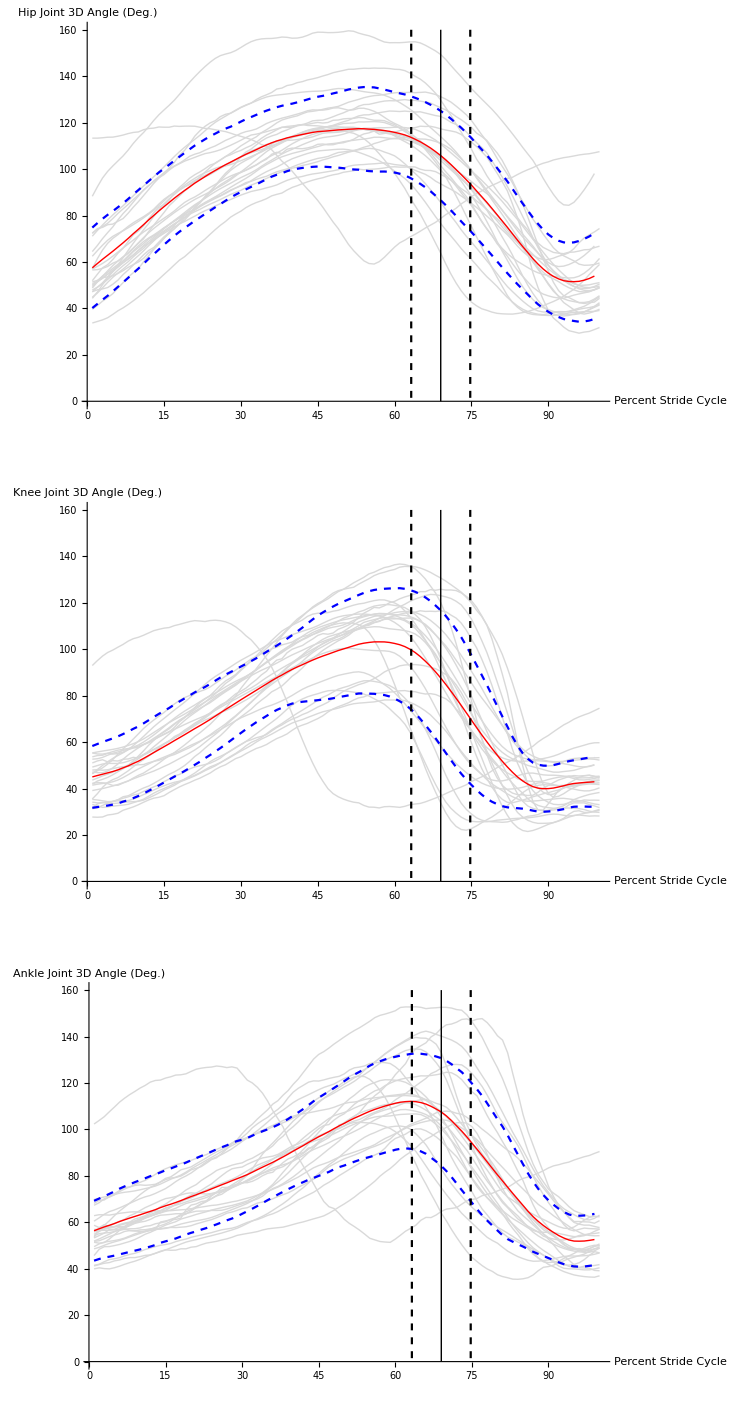

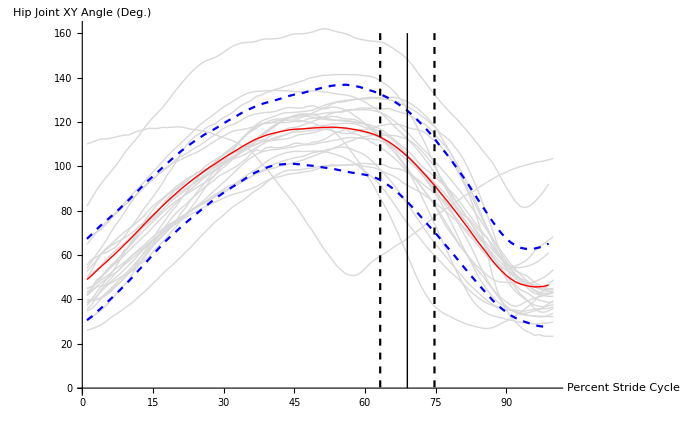

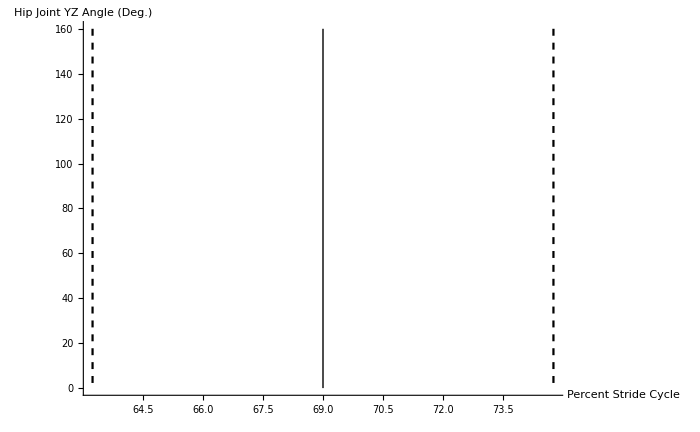

```mathematica
(******************************************************************************************)


(*Hip*)
RSAnimal0Trial1HipPlot=ListLinePlot[RSAnimal0Trial1Hip,PlotStyle->Alltrials];
RSAnimal1Trial1HipPlot=ListLinePlot[RSAnimal1Trial1Hip,PlotStyle->Alltrials];
RSAnimal1Trial2HipPlot=ListLinePlot[RSAnimal1Trial2Hip,PlotStyle->Alltrials];
RSAnimal1Trial3HipPlot=ListLinePlot[RSAnimal1Trial3Hip,PlotStyle->Alltrials];
RSAnimal2Trial1HipPlot=ListLinePlot[RSAnimal2Trial1Hip,PlotStyle->Alltrials];
RSAnimal2Trial2HipPlot=ListLinePlot[RSAnimal2Trial2Hip,PlotStyle->Alltrials];
RSAnimal2Trial3HipPlot=ListLinePlot[RSAnimal2Trial3Hip,PlotStyle->Alltrials];
RSAnimal3Trial1HipPlot=ListLinePlot[RSAnimal3Trial1Hip,PlotStyle->Alltrials];
RSAnimal3Trial2HipPlot=ListLinePlot[RSAnimal3Trial2Hip,PlotStyle->Alltrials];
RSAnimal4Trial1HipPlot=ListLinePlot[RSAnimal4Trial1Hip,PlotStyle->Alltrials];
RSAnimal4Trial2HipPlot=ListLinePlot[RSAnimal4Trial2Hip,PlotStyle->Alltrials];
RSAnimal4Trial3HipPlot=ListLinePlot[RSAnimal4Trial3Hip,PlotStyle->Alltrials];
RSAnimal4Trial4HipPlot=ListLinePlot[RSAnimal4Trial4Hip,PlotStyle->Alltrials];
RSAnimal4Trial5HipPlot=ListLinePlot[RSAnimal4Trial5Hip,PlotStyle->Alltrials];
RSAnimal5Trial1HipPlot=ListLinePlot[RSAnimal5Trial1Hip,PlotStyle->Alltrials];
RSAnimal5Trial2HipPlot=ListLinePlot[RSAnimal5Trial2Hip,PlotStyle->Alltrials];
RSAnimal5Trial3HipPlot=ListLinePlot[RSAnimal5Trial3Hip,PlotStyle->Alltrials];
RSAnimal6Trial1HipPlot=ListLinePlot[RSAnimal6Trial1Hip,PlotStyle->Alltrials];
RSAnimal6Trial2HipPlot=ListLinePlot[RSAnimal6Trial2Hip,PlotStyle->Alltrials];
RSAnimal7Trial1HipPlot=ListLinePlot[RSAnimal7Trial1Hip,PlotStyle->Alltrials];
RSAnimal7Trial2HipPlot=ListLinePlot[RSAnimal7Trial2Hip,PlotStyle->Alltrials];
RSAnimal7Trial3HipPlot=ListLinePlot[RSAnimal7Trial3Hip,PlotStyle->Alltrials];
RSAnimal7Trial4HipPlot=ListLinePlot[RSAnimal7Trial4Hip,PlotStyle->Alltrials];

AllRSAnimal0HipPlot=Show[RSAnimal0Trial1HipPlot];
AllRSAnimal1HipPlot=Show[RSAnimal1Trial1HipPlot,RSAnimal1Trial2HipPlot,RSAnimal1Trial3HipPlot];
AllRSAnimal2HipPlot=Show[RSAnimal2Trial1HipPlot,RSAnimal2Trial2HipPlot,RSAnimal2Trial3HipPlot];
AllRSAnimal3HipPlot=Show[RSAnimal3Trial1HipPlot,RSAnimal3Trial2HipPlot];
AllRSAnimal4HipPlot=Show[RSAnimal4Trial1HipPlot,RSAnimal4Trial2HipPlot,RSAnimal4Trial3HipPlot,RSAnimal4Trial4HipPlot,RSAnimal4Trial5HipPlot];
AllRSAnimal5HipPlot=Show[RSAnimal5Trial1HipPlot,RSAnimal5Trial2HipPlot,RSAnimal5Trial3HipPlot];
AllRSAnimal6HipPlot=Show[RSAnimal6Trial1HipPlot,RSAnimal6Trial2HipPlot,PlotRange->All];
AllRSAnimal7HipPlot=Show[RSAnimal7Trial1HipPlot,RSAnimal7Trial2HipPlot,RSAnimal7Trial3HipPlot,RSAnimal7Trial4HipPlot];
AllRSAnimalsAllTrialsHip=Show[AllRSAnimal0HipPlot,AllRSAnimal1HipPlot,AllRSAnimal2HipPlot,AllRSAnimal3HipPlot,AllRSAnimal4HipPlot,AllRSAnimal5HipPlot,AllRSAnimal6HipPlot,AllRSAnimal7HipPlot,PlotRange->All];

(*Knee*)
RSAnimal0Trial1KneePlot=ListLinePlot[RSAnimal0Trial1Knee,PlotStyle->Alltrials];
RSAnimal1Trial1KneePlot=ListLinePlot[RSAnimal1Trial1Knee,PlotStyle->Alltrials];
RSAnimal1Trial2KneePlot=ListLinePlot[RSAnimal1Trial2Knee,PlotStyle->Alltrials];
RSAnimal1Trial3KneePlot=ListLinePlot[RSAnimal1Trial3Knee,PlotStyle->Alltrials];
RSAnimal2Trial1KneePlot=ListLinePlot[RSAnimal2Trial1Knee,PlotStyle->Alltrials];
RSAnimal2Trial2KneePlot=ListLinePlot[RSAnimal2Trial2Knee,PlotStyle->Alltrials];
RSAnimal2Trial3KneePlot=ListLinePlot[RSAnimal2Trial3Knee,PlotStyle->Alltrials];
RSAnimal3Trial1KneePlot=ListLinePlot[RSAnimal3Trial1Knee,PlotStyle->Alltrials];
RSAnimal3Trial2KneePlot=ListLinePlot[RSAnimal3Trial2Knee,PlotStyle->Alltrials];
RSAnimal4Trial1KneePlot=ListLinePlot[RSAnimal4Trial1Knee,PlotStyle->Alltrials];
RSAnimal4Trial2KneePlot=ListLinePlot[RSAnimal4Trial2Knee,PlotStyle->Alltrials];
RSAnimal4Trial3KneePlot=ListLinePlot[RSAnimal4Trial3Knee,PlotStyle->Alltrials];
RSAnimal4Trial4KneePlot=ListLinePlot[RSAnimal4Trial4Knee,PlotStyle->Alltrials];
RSAnimal4Trial5KneePlot=ListLinePlot[RSAnimal4Trial5Knee,PlotStyle->Alltrials];
RSAnimal5Trial1KneePlot=ListLinePlot[RSAnimal5Trial1Knee,PlotStyle->Alltrials];
RSAnimal5Trial2KneePlot=ListLinePlot[RSAnimal5Trial2Knee,PlotStyle->Alltrials];
RSAnimal5Trial3KneePlot=ListLinePlot[RSAnimal5Trial3Knee,PlotStyle->Alltrials];
RSAnimal6Trial1KneePlot=ListLinePlot[RSAnimal6Trial1Knee,PlotStyle->Alltrials];
RSAnimal6Trial2KneePlot=ListLinePlot[RSAnimal6Trial2Knee,PlotStyle->Alltrials];
RSAnimal7Trial1KneePlot=ListLinePlot[RSAnimal7Trial1Knee,PlotStyle->Alltrials];
RSAnimal7Trial2KneePlot=ListLinePlot[RSAnimal7Trial2Knee,PlotStyle->Alltrials];
RSAnimal7Trial3KneePlot=ListLinePlot[RSAnimal7Trial3Knee,PlotStyle->Alltrials];
RSAnimal7Trial4KneePlot=ListLinePlot[RSAnimal7Trial4Knee,PlotStyle->Alltrials];

AllRSAnimal0KneePlot=Show[RSAnimal0Trial1KneePlot];
AllRSAnimal1KneePlot=Show[RSAnimal1Trial1KneePlot,RSAnimal1Trial2KneePlot,RSAnimal1Trial3KneePlot];
AllRSAnimal2KneePlot=Show[RSAnimal2Trial1KneePlot,RSAnimal2Trial2KneePlot,RSAnimal2Trial3KneePlot];
AllRSAnimal3KneePlot=Show[RSAnimal3Trial1KneePlot,RSAnimal3Trial2KneePlot];
AllRSAnimal4KneePlot=Show[RSAnimal4Trial1KneePlot,RSAnimal4Trial2KneePlot,RSAnimal4Trial3KneePlot,RSAnimal4Trial4KneePlot,RSAnimal4Trial5KneePlot];
AllRSAnimal5KneePlot=Show[RSAnimal5Trial1KneePlot,RSAnimal5Trial2KneePlot,RSAnimal5Trial3KneePlot];
AllRSAnimal6KneePlot=Show[RSAnimal6Trial1KneePlot,RSAnimal6Trial2KneePlot,PlotRange->All];
AllRSAnimal7KneePlot=Show[RSAnimal7Trial1KneePlot,RSAnimal7Trial2KneePlot,RSAnimal7Trial3KneePlot,RSAnimal7Trial4KneePlot];
AllRSAnimalsAllTrialsKnee=Show[AllRSAnimal0KneePlot,AllRSAnimal1KneePlot,AllRSAnimal2KneePlot,AllRSAnimal3KneePlot,AllRSAnimal4KneePlot,AllRSAnimal5KneePlot,AllRSAnimal6KneePlot,AllRSAnimal7KneePlot,PlotRange->All];

(*Ankle*)
RSAnimal0Trial1AnklePlot=ListLinePlot[RSAnimal0Trial1Ankle,PlotStyle->Alltrials];
RSAnimal1Trial1AnklePlot=ListLinePlot[RSAnimal1Trial1Ankle,PlotStyle->Alltrials];
RSAnimal1Trial2AnklePlot=ListLinePlot[RSAnimal1Trial2Ankle,PlotStyle->Alltrials];
RSAnimal1Trial3AnklePlot=ListLinePlot[RSAnimal1Trial3Ankle,PlotStyle->Alltrials];
RSAnimal2Trial1AnklePlot=ListLinePlot[RSAnimal2Trial1Ankle,PlotStyle->Alltrials];
RSAnimal2Trial2AnklePlot=ListLinePlot[RSAnimal2Trial2Ankle,PlotStyle->Alltrials];
RSAnimal2Trial3AnklePlot=ListLinePlot[RSAnimal2Trial3Ankle,PlotStyle->Alltrials];
RSAnimal3Trial1AnklePlot=ListLinePlot[RSAnimal3Trial1Ankle,PlotStyle->Alltrials];
RSAnimal3Trial2AnklePlot=ListLinePlot[RSAnimal3Trial2Ankle,PlotStyle->Alltrials];
RSAnimal4Trial1AnklePlot=ListLinePlot[RSAnimal4Trial1Ankle,PlotStyle->Alltrials];
RSAnimal4Trial2AnklePlot=ListLinePlot[RSAnimal4Trial2Ankle,PlotStyle->Alltrials];
RSAnimal4Trial3AnklePlot=ListLinePlot[RSAnimal4Trial3Ankle,PlotStyle->Alltrials];
RSAnimal4Trial4AnklePlot=ListLinePlot[RSAnimal4Trial4Ankle,PlotStyle->Alltrials];
RSAnimal4Trial5AnklePlot=ListLinePlot[RSAnimal4Trial5Ankle,PlotStyle->Alltrials];
RSAnimal5Trial1AnklePlot=ListLinePlot[RSAnimal5Trial1Ankle,PlotStyle->Alltrials];
RSAnimal5Trial2AnklePlot=ListLinePlot[RSAnimal5Trial2Ankle,PlotStyle->Alltrials];
RSAnimal5Trial3AnklePlot=ListLinePlot[RSAnimal5Trial3Ankle,PlotStyle->Alltrials];
RSAnimal6Trial1AnklePlot=ListLinePlot[RSAnimal6Trial1Ankle,PlotStyle->Alltrials];
RSAnimal6Trial2AnklePlot=ListLinePlot[RSAnimal6Trial2Ankle,PlotStyle->Alltrials];
RSAnimal7Trial1AnklePlot=ListLinePlot[RSAnimal7Trial1Ankle,PlotStyle->Alltrials];
RSAnimal7Trial2AnklePlot=ListLinePlot[RSAnimal7Trial2Ankle,PlotStyle->Alltrials];
RSAnimal7Trial3AnklePlot=ListLinePlot[RSAnimal7Trial3Ankle,PlotStyle->Alltrials];
RSAnimal7Trial4AnklePlot=ListLinePlot[RSAnimal7Trial4Ankle,PlotStyle->Alltrials];

AllRSAnimal0AnklePlot=Show[RSAnimal0Trial1AnklePlot];
AllRSAnimal1AnklePlot=Show[RSAnimal1Trial1AnklePlot,RSAnimal1Trial2AnklePlot,RSAnimal1Trial3AnklePlot];
AllRSAnimal2AnklePlot=Show[RSAnimal2Trial1AnklePlot,RSAnimal2Trial2AnklePlot,RSAnimal2Trial3AnklePlot];
AllRSAnimal3AnklePlot=Show[RSAnimal3Trial1AnklePlot,RSAnimal3Trial2AnklePlot];
AllRSAnimal4AnklePlot=Show[RSAnimal4Trial1AnklePlot,RSAnimal4Trial2AnklePlot,RSAnimal4Trial3AnklePlot,RSAnimal4Trial4AnklePlot,RSAnimal4Trial5AnklePlot];
AllRSAnimal5AnklePlot=Show[RSAnimal5Trial1AnklePlot,RSAnimal5Trial2AnklePlot,RSAnimal5Trial3AnklePlot];
AllRSAnimal6AnklePlot=Show[RSAnimal6Trial1AnklePlot,RSAnimal6Trial2AnklePlot,PlotRange->All];
AllRSAnimal7AnklePlot=Show[RSAnimal7Trial1AnklePlot,RSAnimal7Trial2AnklePlot,RSAnimal7Trial3AnklePlot,RSAnimal7Trial4AnklePlot];
AllRSAnimalsAllTrialsAnkle=Show[AllRSAnimal0AnklePlot,AllRSAnimal1AnklePlot,AllRSAnimal2AnklePlot,AllRSAnimal3AnklePlot,AllRSAnimal4AnklePlot,AllRSAnimal5AnklePlot,AllRSAnimal6AnklePlot,AllRSAnimal7AnklePlot,PlotRange->All];

(*HipXY*)
RSAnimal0Trial1HipXYPlot=ListLinePlot[RSAnimal0Trial1HipXY,PlotStyle->Alltrials];
RSAnimal1Trial1HipXYPlot=ListLinePlot[RSAnimal1Trial1HipXY,PlotStyle->Alltrials];
RSAnimal1Trial2HipXYPlot=ListLinePlot[RSAnimal1Trial2HipXY,PlotStyle->Alltrials];
RSAnimal1Trial3HipXYPlot=ListLinePlot[RSAnimal1Trial3HipXY,PlotStyle->Alltrials];
RSAnimal2Trial1HipXYPlot=ListLinePlot[RSAnimal2Trial1HipXY,PlotStyle->Alltrials];
RSAnimal2Trial2HipXYPlot=ListLinePlot[RSAnimal2Trial2HipXY,PlotStyle->Alltrials];
RSAnimal2Trial3HipXYPlot=ListLinePlot[RSAnimal2Trial3HipXY,PlotStyle->Alltrials];
RSAnimal3Trial1HipXYPlot=ListLinePlot[RSAnimal3Trial1HipXY,PlotStyle->Alltrials];
RSAnimal3Trial2HipXYPlot=ListLinePlot[RSAnimal3Trial2HipXY,PlotStyle->Alltrials];
RSAnimal4Trial1HipXYPlot=ListLinePlot[RSAnimal4Trial1HipXY,PlotStyle->Alltrials];
RSAnimal4Trial2HipXYPlot=ListLinePlot[RSAnimal4Trial2HipXY,PlotStyle->Alltrials];
RSAnimal4Trial3HipXYPlot=ListLinePlot[RSAnimal4Trial3HipXY,PlotStyle->Alltrials];
RSAnimal4Trial4HipXYPlot=ListLinePlot[RSAnimal4Trial4HipXY,PlotStyle->Alltrials];
RSAnimal4Trial5HipXYPlot=ListLinePlot[RSAnimal4Trial5HipXY,PlotStyle->Alltrials];
RSAnimal5Trial1HipXYPlot=ListLinePlot[RSAnimal5Trial1HipXY,PlotStyle->Alltrials];
RSAnimal5Trial2HipXYPlot=ListLinePlot[RSAnimal5Trial2HipXY,PlotStyle->Alltrials];
RSAnimal5Trial3HipXYPlot=ListLinePlot[RSAnimal5Trial3HipXY,PlotStyle->Alltrials];
RSAnimal6Trial1HipXYPlot=ListLinePlot[RSAnimal6Trial1HipXY,PlotStyle->Alltrials];
RSAnimal6Trial2HipXYPlot=ListLinePlot[RSAnimal6Trial2HipXY,PlotStyle->Alltrials];
RSAnimal7Trial1HipXYPlot=ListLinePlot[RSAnimal7Trial1HipXY,PlotStyle->Alltrials];
RSAnimal7Trial2HipXYPlot=ListLinePlot[RSAnimal7Trial2HipXY,PlotStyle->Alltrials];
RSAnimal7Trial3HipXYPlot=ListLinePlot[RSAnimal7Trial3HipXY,PlotStyle->Alltrials];
RSAnimal7Trial4HipXYPlot=ListLinePlot[RSAnimal7Trial4HipXY,PlotStyle->Alltrials];

AllRSAnimal0HipXYPlot=Show[RSAnimal0Trial1HipXYPlot];
AllRSAnimal1HipXYPlot=Show[RSAnimal1Trial1HipXYPlot,RSAnimal1Trial2HipXYPlot,RSAnimal1Trial3HipXYPlot];
AllRSAnimal2HipXYPlot=Show[RSAnimal2Trial1HipXYPlot,RSAnimal2Trial2HipXYPlot,RSAnimal2Trial3HipXYPlot];
AllRSAnimal3HipXYPlot=Show[RSAnimal3Trial1HipXYPlot,RSAnimal3Trial2HipXYPlot];
AllRSAnimal4HipXYPlot=Show[RSAnimal4Trial1HipXYPlot,RSAnimal4Trial2HipXYPlot,RSAnimal4Trial3HipXYPlot,RSAnimal4Trial4HipXYPlot,RSAnimal4Trial5HipXYPlot];
AllRSAnimal5HipXYPlot=Show[RSAnimal5Trial1HipXYPlot,RSAnimal5Trial2HipXYPlot,RSAnimal5Trial3HipXYPlot];
AllRSAnimal6HipXYPlot=Show[RSAnimal6Trial1HipXYPlot,RSAnimal6Trial2HipXYPlot,PlotRange->All];
AllRSAnimal7HipXYPlot=Show[RSAnimal7Trial1HipXYPlot,RSAnimal7Trial2HipXYPlot,RSAnimal7Trial3HipXYPlot,RSAnimal7Trial4HipXYPlot];
AllRSAnimalsAllTrialsHipXY=Show[AllRSAnimal0HipXYPlot,AllRSAnimal1HipXYPlot,AllRSAnimal2HipXYPlot,AllRSAnimal3HipXYPlot,AllRSAnimal4HipXYPlot,AllRSAnimal5HipXYPlot,AllRSAnimal6HipXYPlot,AllRSAnimal7HipXYPlot,PlotRange->All];

(*HipYZ*)
RSAnimal0Trial1HipYZPlot=ListLinePlot[RSAnimal0Trial1HipYZ,PlotStyle->Alltrials];
RSAnimal1Trial1HipYZPlot=ListLinePlot[RSAnimal1Trial1HipYZ,PlotStyle->Alltrials];
RSAnimal1Trial2HipYZPlot=ListLinePlot[RSAnimal1Trial2HipYZ,PlotStyle->Alltrials];
RSAnimal1Trial3HipYZPlot=ListLinePlot[RSAnimal1Trial3HipYZ,PlotStyle->Alltrials];
RSAnimal2Trial1HipYZPlot=ListLinePlot[RSAnimal2Trial1HipYZ,PlotStyle->Alltrials];
RSAnimal2Trial2HipYZPlot=ListLinePlot[RSAnimal2Trial2HipYZ,PlotStyle->Alltrials];
RSAnimal2Trial3HipYZPlot=ListLinePlot[RSAnimal2Trial3HipYZ,PlotStyle->Alltrials];
RSAnimal3Trial1HipYZPlot=ListLinePlot[RSAnimal3Trial1HipYZ,PlotStyle->Alltrials];
RSAnimal3Trial2HipYZPlot=ListLinePlot[RSAnimal3Trial2HipYZ,PlotStyle->Alltrials];
RSAnimal4Trial1HipYZPlot=ListLinePlot[RSAnimal4Trial1HipYZ,PlotStyle->Alltrials];
RSAnimal4Trial2HipYZPlot=ListLinePlot[RSAnimal4Trial2HipYZ,PlotStyle->Alltrials];
RSAnimal4Trial3HipYZPlot=ListLinePlot[RSAnimal4Trial3HipYZ,PlotStyle->Alltrials];
RSAnimal4Trial4HipYZPlot=ListLinePlot[RSAnimal4Trial4HipYZ,PlotStyle->Alltrials];
RSAnimal4Trial5HipYZPlot=ListLinePlot[RSAnimal4Trial5HipYZ,PlotStyle->Alltrials];
RSAnimal5Trial1HipYZPlot=ListLinePlot[RSAnimal5Trial1HipYZ,PlotStyle->Alltrials];
RSAnimal5Trial2HipYZPlot=ListLinePlot[RSAnimal5Trial2HipYZ,PlotStyle->Alltrials];
RSAnimal5Trial3HipYZPlot=ListLinePlot[RSAnimal5Trial3HipYZ,PlotStyle->Alltrials];
RSAnimal6Trial1HipYZPlot=ListLinePlot[RSAnimal6Trial1HipYZ,PlotStyle->Alltrials];
RSAnimal6Trial2HipYZPlot=ListLinePlot[RSAnimal6Trial2HipYZ,PlotStyle->Alltrials];
RSAnimal7Trial1HipYZPlot=ListLinePlot[RSAnimal7Trial1HipYZ,PlotStyle->Alltrials];
RSAnimal7Trial2HipYZPlot=ListLinePlot[RSAnimal7Trial2HipYZ,PlotStyle->Alltrials];
RSAnimal7Trial3HipYZPlot=ListLinePlot[RSAnimal7Trial3HipYZ,PlotStyle->Alltrials];
RSAnimal7Trial4HipYZPlot=ListLinePlot[RSAnimal7Trial4HipYZ,PlotStyle->Alltrials];

AllRSAnimal0HipYZPlot=Show[RSAnimal0Trial1HipYZPlot];
AllRSAnimal1HipYZPlot=Show[RSAnimal1Trial1HipYZPlot,RSAnimal1Trial2HipYZPlot,RSAnimal1Trial3HipYZPlot];
AllRSAnimal2HipYZPlot=Show[RSAnimal2Trial1HipYZPlot,RSAnimal2Trial2HipYZPlot,RSAnimal2Trial3HipYZPlot];
AllRSAnimal3HipYZPlot=Show[RSAnimal3Trial1HipYZPlot,RSAnimal3Trial2HipYZPlot];
AllRSAnimal4HipYZPlot=Show[RSAnimal4Trial1HipYZPlot,RSAnimal4Trial2HipYZPlot,RSAnimal4Trial3HipYZPlot,RSAnimal4Trial4HipYZPlot,RSAnimal4Trial5HipYZPlot];
AllRSAnimal5HipYZPlot=Show[RSAnimal5Trial1HipYZPlot,RSAnimal5Trial2HipYZPlot,RSAnimal5Trial3HipYZPlot];
AllRSAnimal6HipYZPlot=Show[RSAnimal6Trial1HipYZPlot,RSAnimal6Trial2HipYZPlot,PlotRange->All];
AllRSAnimal7HipYZPlot=Show[RSAnimal7Trial1HipYZPlot,RSAnimal7Trial2HipYZPlot,RSAnimal7Trial3HipYZPlot,RSAnimal7Trial4HipYZPlot];
AllRSAnimalsAllTrialsHipYZ=Show[AllRSAnimal0HipYZPlot,AllRSAnimal1HipYZPlot,AllRSAnimal2HipYZPlot,AllRSAnimal3HipYZPlot,AllRSAnimal4HipYZPlot,AllRSAnimal5HipYZPlot,AllRSAnimal6HipYZPlot,AllRSAnimal7HipYZPlot,PlotRange->All];



(*Hip*)
MeanSDHipjointAnglePlot=Show[AllRSAnimalsAllTrialsHip,MeanHipjointAnglePlot,PlusSDHipjointAnglePlot,MinusSDHipjointAnglePlot,MeanSDPSCStartofSwingPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Hip Joint 3D Angle (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700];

(*Knee*)
MeanSDKneejointAnglePlot=Show[AllRSAnimalsAllTrialsKnee,MeanKneejointAnglePlot,PlusSDKneejointAnglePlot,MinusSDKneejointAnglePlot,MeanSDPSCStartofSwingPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Knee Joint 3D Angle (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700];

(*Ankle*)
MeanSDAnklejointAnglePlot=Show[AllRSAnimalsAllTrialsAnkle,MeanAnklejointAnglePlot,PlusSDAnklejointAnglePlot,MinusSDAnklejointAnglePlot,MeanSDPSCStartofSwingPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Ankle Joint 3D Angle (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700];

GraphicsColumn[{MeanSDHipjointAnglePlot,MeanSDKneejointAnglePlot,MeanSDAnklejointAnglePlot}]

(*HipXY*)
MeanSDHipXYjointAnglePlot=Show[AllRSAnimalsAllTrialsHipXY,MeanHipXYjointAnglePlot,PlusSDHipXYjointAnglePlot,MinusSDHipXYjointAnglePlot,MeanSDPSCStartofSwingPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Hip Joint XY Angle (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700]

(*(*HipYZ*)
MeanSDHipYZjointAnglePlot=Show[AllRSAnimalsAllTrialsHipYZ,MeanHipYZjointAnglePlot,PlusSDHipYZjointAnglePlot,MinusSDHipYZjointAnglePlot,MeanSDPSCStartofSwingPlot,PlotRange->MeanSDplotrange,AxesLabel->{"Percent Stride Cycle","Hip Joint YZ Angle (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700]

GraphicsColumn[{MeanSDHipXYjointAnglePlot,MeanSDHipYZjointAnglePlot}];*)
```

```mathematica
(*****************************************************************************************************)
(*****************************************************************************************************)
```

```mathematica
(*EXPORT*)
(*Export the images*)

dataDirectory="YOUR DIRECTORY FOR EXPORTED FIGURES";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];


Export["Kinematics Paper - Mean plus.minus SD Hip Joint 3D Angle Plot.svg",MeanSDHipjointAnglePlot];
Export["Kinematics Paper - Mean plus.minus SD Knee Joint 3D Angle Plot.svg",MeanSDKneejointAnglePlot];
Export["Kinematics Paper - Mean plus.minus SD Ankle Joint 3D Angle Plot.svg",MeanSDAnklejointAnglePlot];
Export["Kinematics Paper - Mean plus.minus SD Hip XY Joint Angle Plot.svg",MeanSDHipXYjointAnglePlot];

Print["EXPORTED"]
```

EXPORTED